# Steam-Punk Lambda: General Computation with 4x4 Matrices

## Brian Beckman, Erik Meijer, David Leibs Dec 2012 Brisbane, Australia

Can we do arbitrary computations using only primitive operations on 4x4 matrices? We'd like that since we might be able to run them on a GPU. The idea is to compile ordinary code -- say C++ code or Java code, etc. -- to operations on 4x4 matrices, as if that were the instruction set of our machine. Contrast this against OpenACC or CUDA, which are basically DSLs for the GPU embedded in ordinary programming languages. Those give you ways to write code specifically for the GPU using your favorite language -- C++ or Java, etc. We want a way to write ordinary code -- not necessarily machine-sympathetic -- and compile it so that it runs in the GPU.

The allowed primitive operations are matrix multiply, transpose, addition.

## PUNKS AND SKAS

A [PUNK] is a 4x4 matrix. A [SKA] is a 2x2 block in a punk. There are four skas in a punk: [UL], [UR], [LL], and [LR] (upper-left, upper-right, lower-left, lower-right)

### Symbolic Punks

Here are a few punks to use in our investigataions.

```mathematica
script[c_]:=Quiet@ToExpression["\\[Script"<>"Capital"<>ToUpperCase[ToString[c]]<>"]"]
```

```mathematica
double[c_]:=Quiet@ToExpression["\\[DoubleStruck"<>"Capital"<>ToUpperCase[ToString[c]]<>"]"]
```

```mathematica
greek[c_]:=Quiet@ToExpression[ToString[c]/.{"a"->α,"b"->β,"c"->γ,"d"->δ,"e"->ϵ,"f"->ϕ,"g"->χ,"h"->η,"i"->ι,"j"->φ,"k"->κ,"l"->λ,"m"->μ,"n"->ν,"o"->ο,"p"->π,"q"->θ,"r"->ρ,"s"->σ,"t"->τ,"u"->υ,"w"->ω,"x"->ξ,"y"->ψ,"z"->ζ}]
```

```mathematica
pv[ul_,ur_,ll_,lr_]:=({{ul, ur, greek@ul, greek@ur}, {ll, lr, greek@ll, greek@lr}, {script@ul, script@ur, double@ul, double@ur}, {script@ll, script@lr, double@ll, double@lr}})
```

```mathematica
Grid@{MatrixForm/@
{p=pv[a,b,c,d],
q=pv[x,y,z,w]}}
```

(a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻) | (x | y | ξ | ψ
z | w | ζ | ω
𝒳 | 𝒴 | 𝕏 | 𝕐
𝒵 | 𝒲 | ℤ | 𝕎)

### Standard display ideas from the "Insert" menu

The standard display idea is just MatrixForm. The "Insert" menu produces a mysterious, covert object that the notebook front-end knows how to display but that has no obvious overt FullForm representation, meaning I don't know how to construct one of these without the menu and I don't know how to set its options, if it has any. This means that we must find another way to display punks in the way we like.

### New display ideas from the @SE chat room

Thanks to Rojo @Mathematica.stackexchange.com for these ideas.

```mathematica
dpy[punk_]:=Grid[punk,Dividers->{{{True,False}},{{True,False}}}];
dpy[p]
```

a | b | α | β
c | d | γ | δ
𝒜 | ℬ | 𝔸 | 𝔹
𝒞 | 𝒟 | ℂ | 𝔻

```mathematica
ClearAll[dpy];
dpy[punk_List]:=
Grid[Map[TableForm[#,TableSpacing->{0.,0.25},TableAlignments->Center]&,Partition[punk,{2,2}],{2}],Frame->All];
dpy[x_]:=x (* dpy should be hippocratic *)
dpy@p
```

a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻

### The UL ska is special

Divide punks into equivalence classes:

All punks with the same UL-ska are equivalent -- they all represent the same value in the system. The contents of the other three skas are "machine-state," but the value of the punk as a whole is just the value of the upper-left ska.

The prime representative of an equivalence class is the [CHIEF] of that class. It has the same UL-ska as every other member of the class, but zeros elsewhere. To test whether two punks are equivalent, compare their chiefs.

The [MACHINE-STATE] of a punk ßis the contents of all skas other than the UL-ska.

## PRIMITIVE PUNKS

```mathematica
ill=({{0, 0, 0, 0}, {0, 0, 0, 0}, {1, 0, 0, 0}, {0, 1, 0, 0}});iul=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});iur=({{0, 0, 1, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}, {0, 0, 0, 0}});ilr=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});
```

### REGISTERS

```mathematica
registers={iul,iur,ill,ilr};
```

UL is like EAX in the x86 machine: it's a special register where you can find the result of a computation and where you expect the value of an actual argument to a unary function to appear. Another analogy is with HP calculators, in which the x register is special -- it holds preferred arguments and the results of operations.

In this analogy, four registers of the original HP calculators are mapped as follows: {UL -> x, UR -> y, LR -> z, LL -> t}.

```mathematica
inf=({{Infinity, 0, 0, 0}, {0, Infinity, 0, 0}, {0, 0, Infinity, 0}, {0, 0, 0, Infinity}});
```

### Booleans

```mathematica
falsePunk=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});truePunk=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});
```

truePunk composed with any matrix is that matrix

```mathematica
truePunk.p===p
```

True

falsePunk annihilates any matrix

```mathematica
falsePunk.p===falsePunk
```

True

A falsey matrix is one whose CHIEF matches the false matrix

```mathematica
falsey[m_]:=CHF[m]===falsePunk
```

A truthy matrix is one whose CHIEF is not falsey

```mathematica
truthy[m_]:=CHF[m]=!=falsePunk
```

The other registers don't matter when testing truthiness or falseyness

```mathematica
(truthy[MV[#,p]])&/@registers
```

{True,True,True,True}

```mathematica
(falsey[MV[#,p]])&/@registers
```

{False,False,False,False}

Convenience:

```mathematica
ClearAll[T,M];
T=Transpose;M=dpy;
gridStack[stack_]:=Grid[{M/@stack},Frame->All];
```

Investigate what any particular operator does to a sample punk in various combinations, namely conjugators, m.p.m^T, m^T.p.m, commutators, m.p.m^T.p^T, and so on:

```mathematica
combos[m_,p_]:=With[{mT=m//T,pT=p//T},
Grid[{
M/@{m.p,p.mT,m.p.mT(*,m.p.mT.pT,p.m.pT.mT,mT.p.m.pT*)},
M/@{mT.p,p.m,mT.p.m(*,mT.pT.m.p,p.mT.pT,m.pT.mT.p*)}
}]];
```

```mathematica
combos[iur,p]
```

𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻
0 | 0
0 | 0 | 0 | 0
0 | 0 | α | β
γ | δ | 0 | 0
0 | 0
𝔸 | 𝔹
ℂ | 𝔻 | 0 | 0
0 | 0 | 𝔸 | 𝔹
ℂ | 𝔻 | 0 | 0
0 | 0
0 | 0
0 | 0 | 0 | 0
0 | 0
0 | 0
0 | 0 | 0 | 0
0 | 0
a | b
c | d | α | β
γ | δ | 0 | 0
0 | 0 | a | b
c | d
0 | 0
0 | 0 | 𝒜 | ℬ
𝒞 | 𝒟 | 0 | 0
0 | 0 | 0 | 0
0 | 0
0 | 0
0 | 0 | a | b
c | d

```mathematica
combos[ilr,p]
```

0 | 0
0 | 0 | 0 | 0
0 | 0
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻 | 0 | 0
0 | 0 | α | β
γ | δ
0 | 0
0 | 0 | 𝔸 | 𝔹
ℂ | 𝔻 | 0 | 0
0 | 0 | 0 | 0
0 | 0
0 | 0
0 | 0 | 𝔸 | 𝔹
ℂ | 𝔻
0 | 0
0 | 0 | 0 | 0
0 | 0
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻 | 0 | 0
0 | 0 | α | β
γ | δ
0 | 0
0 | 0 | 𝔸 | 𝔹
ℂ | 𝔻 | 0 | 0
0 | 0 | 0 | 0
0 | 0
0 | 0
0 | 0 | 𝔸 | 𝔹
ℂ | 𝔻

```mathematica
combos[ill,p]
```

0 | 0
0 | 0 | 0 | 0
0 | 0
a | b
c | d | α | β
γ | δ | 0 | 0
0 | 0 | a | b
c | d
0 | 0
0 | 0 | 𝒜 | ℬ
𝒞 | 𝒟 | 0 | 0
0 | 0 | 0 | 0
0 | 0
0 | 0
0 | 0 | a | b
c | d
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻
0 | 0
0 | 0 | 0 | 0
0 | 0 | α | β
γ | δ | 0 | 0
0 | 0
𝔸 | 𝔹
ℂ | 𝔻 | 0 | 0
0 | 0 | 𝔸 | 𝔹
ℂ | 𝔻 | 0 | 0
0 | 0
0 | 0
0 | 0 | 0 | 0
0 | 0

```mathematica
combos[iul,p]
```

a | b
c | d | α | β
γ | δ
0 | 0
0 | 0 | 0 | 0
0 | 0 | a | b
c | d | 0 | 0
0 | 0
𝒜 | ℬ
𝒞 | 𝒟 | 0 | 0
0 | 0 | a | b
c | d | 0 | 0
0 | 0
0 | 0
0 | 0 | 0 | 0
0 | 0
a | b
c | d | α | β
γ | δ
0 | 0
0 | 0 | 0 | 0
0 | 0 | a | b
c | d | 0 | 0
0 | 0
𝒜 | ℬ
𝒞 | 𝒟 | 0 | 0
0 | 0 | a | b
c | d | 0 | 0
0 | 0
0 | 0
0 | 0 | 0 | 0
0 | 0

## SIMULATE HP-CALCULATOR

Here are some macros that will let me simulate a stack machine inside the matrices.

-Graphics-

-Graphics-

### MVxx

I can move the CHIEF in the upper left corner into any one of the four registers. This is NOT hippocratic. It throws if given an illegal register name.

```mathematica
ClearAll[MV,MVUL,MVUR,MVLR,MVLL];
MV[reg_,m_]:=
((*Print["MV: "<>ToString@reg];*)
If[Not[MemberQ[registers,reg]],Throw["MV: NO NO NO"],
reg/.{
iul->iul.m.(iul//T),
iur->iul.m.(ill//T),
ill->ill.m.(iul//T),
ilr->ill.m.(ill//T)
}]);
MVUL[m_]:=MV[iul,m];
MVUR[m_]:=MV[iur,m];
MVLR[m_]:=MV[ilr,m];
MVLL[m_]:=MV[ill,m];
```

```mathematica
Grid[{(MV[#,p]//M)&/@registers}]
```

a | b
c | d | 0 | 0
0 | 0
0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | a | b
c | d
0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0
a | b
c | d | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0
0 | 0
0 | 0 | a | b
c | d

### AMV

Move any one of the four registers into ul, the CHIEF position.

```mathematica
ClearAll[AMV,AMVUL,AMVUR,AMVLR,AMVLL];
AMV[reg_,m_]:=
((*Print["AMV: "<>ToString@reg];*)
If[Not[MemberQ[registers,reg]],Throw["AMV: NO NO NO"],
reg/.{iul->(iul//T).m.iul,
iur->(iul//T).m.ill,
ill->(ill//T).m.iul,
ilr->(ill//T).m.ill
}]);
AMVUL[m_]:=AMV[iul,m];
AMVUR[m_]:=AMV[iur,m];
AMVLR[m_]:=AMV[ilr,m];
AMVLL[m_]:=AMV[ill,m];
```

```mathematica
Grid[{(AMV[#,p]//M)&/@registers}]
```

a | b
c | d | 0 | 0
0 | 0
0 | 0
0 | 0 | 0 | 0
0 | 0 | α | β
γ | δ | 0 | 0
0 | 0
0 | 0
0 | 0 | 0 | 0
0 | 0 | 𝒜 | ℬ
𝒞 | 𝒟 | 0 | 0
0 | 0
0 | 0
0 | 0 | 0 | 0
0 | 0 | 𝔸 | 𝔹
ℂ | 𝔻 | 0 | 0
0 | 0
0 | 0
0 | 0 | 0 | 0
0 | 0

### CY

Move whatever is in r2 into r1, destroying machine state along the way.

```mathematica
CY[r1_,r2_,m_]:=MV[r1,AMV[r2,m]]
```

```mathematica
Grid@{M/@{CY[iul,ilr,p],CY[ilr,iul,p]}}
```

𝔸 | 𝔹
ℂ | 𝔻 | 0 | 0
0 | 0
0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0
0 | 0
0 | 0 | a | b
c | d

```mathematica
Grid@(Outer[M@CY[#1,#2,p]&,registers,registers,1])
```

a | b
c | d | 0 | 0
0 | 0
0 | 0
0 | 0 | 0 | 0
0 | 0 | α | β
γ | δ | 0 | 0
0 | 0
0 | 0
0 | 0 | 0 | 0
0 | 0 | 𝒜 | ℬ
𝒞 | 𝒟 | 0 | 0
0 | 0
0 | 0
0 | 0 | 0 | 0
0 | 0 | 𝔸 | 𝔹
ℂ | 𝔻 | 0 | 0
0 | 0
0 | 0
0 | 0 | 0 | 0
0 | 0
0 | 0
0 | 0 | a | b
c | d
0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | α | β
γ | δ
0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 𝒜 | ℬ
𝒞 | 𝒟
0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 𝔸 | 𝔹
ℂ | 𝔻
0 | 0
0 | 0 | 0 | 0
0 | 0
0 | 0
0 | 0 | 0 | 0
0 | 0
a | b
c | d | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0
α | β
γ | δ | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0
𝒜 | ℬ
𝒞 | 𝒟 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0
𝔸 | 𝔹
ℂ | 𝔻 | 0 | 0
0 | 0
0 | 0
0 | 0 | 0 | 0
0 | 0
0 | 0
0 | 0 | a | b
c | d | 0 | 0
0 | 0 | 0 | 0
0 | 0
0 | 0
0 | 0 | α | β
γ | δ | 0 | 0
0 | 0 | 0 | 0
0 | 0
0 | 0
0 | 0 | 𝒜 | ℬ
𝒞 | 𝒟 | 0 | 0
0 | 0 | 0 | 0
0 | 0
0 | 0
0 | 0 | 𝔸 | 𝔹
ℂ | 𝔻

### CHF

Extract the CHIEF of any matrix by masking off the MACHINE-STATE portion

```mathematica
CHF[m_]:=iul.m.(iul//T);
```

```mathematica
CHF[p]//M
```

a | b
c | d | 0 | 0
0 | 0
0 | 0
0 | 0 | 0 | 0
0 | 0

### ST

Extract the MACHINE-STATE from any matrix -- the ANTI-CHIEF

```mathematica
ST[m_]:=m-CHF[m]
```

```mathematica
ST[p]//M
```

0 | 0
0 | 0 | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻

### ROTC -- like Roll Down

Rotate All skas clockwise within a punk

```mathematica
ClearAll[show];
show[punk_,op_]:=Grid@{M/@{punk,"⟶",op@punk}}
```

```mathematica
ClearAll[ROTC];
ROTC[m_]:=CY[iul,ill,m]+CY[iur,iul,m]+CY[ilr,iur,m]+CY[ill,ilr,m]
```

```mathematica
show[q,ROTC]
```

x | y
z | w | ξ | ψ
ζ | ω
𝒳 | 𝒴
𝒵 | 𝒲 | 𝕏 | 𝕐
ℤ | 𝕎 | ⟶ | 𝒳 | 𝒴
𝒵 | 𝒲 | x | y
z | w
𝕏 | 𝕐
ℤ | 𝕎 | ξ | ψ
ζ | ω

### ROTU -- like Roll Up

```mathematica
ClearAll[ROTU];
ROTU[m_]:=CY[iul,iur,m]+CY[iur,ilr,m]+CY[ilr,ill,m]+CY[ill,iul,m]
```

```mathematica
show[q,ROTU]
```

x | y
z | w | ξ | ψ
ζ | ω
𝒳 | 𝒴
𝒵 | 𝒲 | 𝕏 | 𝕐
ℤ | 𝕎 | ⟶ | ξ | ψ
ζ | ω | 𝕏 | 𝕐
ℤ | 𝕎
x | y
z | w | 𝒳 | 𝒴
𝒵 | 𝒲

### DUP -- like ENTER

```mathematica
DUP[m_]:=ST@ROTC@m+CHF@m
```

```mathematica
show[q,DUP]
```

x | y
z | w | ξ | ψ
ζ | ω
𝒳 | 𝒴
𝒵 | 𝒲 | 𝕏 | 𝕐
ℤ | 𝕎 | ⟶ | x | y
z | w | x | y
z | w
𝕏 | 𝕐
ℤ | 𝕎 | ξ | ψ
ζ | ω

### PLUS

Add UL and UR; drop "down" (counterclockwise) the stack non-destructively, that is, replicating LL into LR.

UL <-- UL+UR; UR <-- LR; LR <-- LL; LL <-- LL

```mathematica
PLUS[m_]:=CHF@m+AMV[iur,m]+CY[iur,ilr,m]+CY[ilr,ill,m]+CY[ill,ill,m]
```

```mathematica
show[q,PLUS]
```

x | y
z | w | ξ | ψ
ζ | ω
𝒳 | 𝒴
𝒵 | 𝒲 | 𝕏 | 𝕐
ℤ | 𝕎 | ⟶ | x+ξ | y+ψ
z+ζ | w+ω | 𝕏 | 𝕐
ℤ | 𝕎
𝒳 | 𝒴
𝒵 | 𝒲 | 𝒳 | 𝒴
𝒵 | 𝒲

### MINUS

```mathematica
MINUS[m_]:=CHF@m-AMV[iur,m]+CY[iur,ilr,m]+CY[ilr,ill,m]+CY[ill,ill,m]
```

```mathematica
show[q,MINUS]
```

x | y
z | w | ξ | ψ
ζ | ω
𝒳 | 𝒴
𝒵 | 𝒲 | 𝕏 | 𝕐
ℤ | 𝕎 | ⟶ | x-ξ | y-ψ
z-ζ | w-ω | 𝕏 | 𝕐
ℤ | 𝕎
𝒳 | 𝒴
𝒵 | 𝒲 | 𝒳 | 𝒴
𝒵 | 𝒲

### TIMES

```mathematica
TIMES[m_]:=CHF[m].AMV[iur,m]+CY[iur,ilr,m]+CY[ilr,ill,m]+CY[ill,ill,m]
```

```mathematica
show[q,TIMES]
```

x | y
z | w | ξ | ψ
ζ | ω
𝒳 | 𝒴
𝒵 | 𝒲 | 𝕏 | 𝕐
ℤ | 𝕎 | ⟶ | y ζ+x ξ | x ψ+y ω
w ζ+z ξ | z ψ+w ω | 𝕏 | 𝕐
ℤ | 𝕎
𝒳 | 𝒴
𝒵 | 𝒲 | 𝒳 | 𝒴
𝒵 | 𝒲

### TRANS

```mathematica
TRANS[m_]:=T@CHF@m+ST@m
```

```mathematica
show[q,TRANS]
```

x | y
z | w | ξ | ψ
ζ | ω
𝒳 | 𝒴
𝒵 | 𝒲 | 𝕏 | 𝕐
ℤ | 𝕎 | ⟶ | x | z
y | w | ξ | ψ
ζ | ω
𝒳 | 𝒴
𝒵 | 𝒲 | 𝕏 | 𝕐
ℤ | 𝕎

### SWAP

```mathematica
SWAP[m_]:=MV[iur,m]+AMV[iur,m]+ilr.m
```

```mathematica
show[q,SWAP]
```

x | y
z | w | ξ | ψ
ζ | ω
𝒳 | 𝒴
𝒵 | 𝒲 | 𝕏 | 𝕐
ℤ | 𝕎 | ⟶ | ξ | ψ
ζ | ω | x | y
z | w
𝒳 | 𝒴
𝒵 | 𝒲 | 𝕏 | 𝕐
ℤ | 𝕎

### COND

If the chief is zero, AMV[LR], if chief is Identity[2] AMV[UR], else garbage

UL.LR - (UL - I2).UR

```mathematica
ClearAll[trueTemp];(trueTemp[m_]:=(iul+ST@m))//M
ClearAll[falseTemp];(falseTemp[m_]:=(ST@m))//M
```

```mathematica
gridStack@{trueTemp@q,falseTemp@q}
```

1 | 0
0 | 1 | ξ | ψ
ζ | ω
𝒳 | 𝒴
𝒵 | 𝒲 | 𝕏 | 𝕐
ℤ | 𝕎 | 0 | 0
0 | 0 | ξ | ψ
ζ | ω
𝒳 | 𝒴
𝒵 | 𝒲 | 𝕏 | 𝕐
ℤ | 𝕎

```mathematica
COND[m_]:=TIMES@m-TIMES@ROTC@SWAP@ROTU@(m-iul)
```

```mathematica
COND/@{trueTemp@q,falseTemp@q}//gridStack
```

ξ | ψ
ζ | ω | 𝕏-ξ | 𝕐-ψ
ℤ-ζ | 𝕎-ω
0 | 0
0 | 0 | 0 | 0
0 | 0 | 𝕏 | 𝕐
ℤ | 𝕎 | 𝕏-ξ | 𝕐-ψ
ℤ-ζ | 𝕎-ω
0 | 0
0 | 0 | 0 | 0
0 | 0

### NAND

```mathematica
NAND[m_]:=TIMES@m
```

```mathematica
(NAND@p)//M
```

a α+b γ | a β+b δ
c α+d γ | c β+d δ | 𝔸 | 𝔹
ℂ | 𝔻
𝒜 | ℬ
𝒞 | 𝒟 | 𝒜 | ℬ
𝒞 | 𝒟

```mathematica
ClearAll[fish,tt,tf,ft,ff];
fish={CHF,dot,iul,AMV,iul,plus,ill,iul,CY,ill,AMV};
clear[];tt=exec[{p,q}~Join~fish];
clear[];tf=exec[{p,ST@p}~Join~fish];
clear[];ft=exec[{ST@p,q}~Join~fish];
clear[];ff=exec[{ST@p,ST@q}~Join~fish];
Grid[MapThread[Map,{{pretty[{#}]&,falsey[#⟦1⟧]&,Length},Table[{tt,tf,ft,ff},{3}]}]]
```

### EQUAL (UNDONE)

If UL and UR are equal, leave I2 in UL, else leave 02.

```mathematica
EQUAL[m_]:=iul+MINUS@m-(CHF@(iul-MINUS@m))
```

```mathematica
M/@((iul+MINUS@#)&/@{q,DUP@q})
```

{1+x-ξ | y-ψ
z-ζ | 1+w-ω | 𝕏 | 𝕐
ℤ | 𝕎
𝒳 | 𝒴
𝒵 | 𝒲 | 𝒳 | 𝒴
𝒵 | 𝒲,1 | 0
0 | 1 | ξ | ψ
ζ | ω
𝕏 | 𝕐
ℤ | 𝕎 | 𝕏 | 𝕐
ℤ | 𝕎}

```mathematica
M/@((iul+MINUS@#)&/@{q,DUP@q})
```

{1+x-ξ | y-ψ
z-ζ | 1+w-ω | 𝕏 | 𝕐
ℤ | 𝕎
𝒳 | 𝒴
𝒵 | 𝒲 | 𝒳 | 𝒴
𝒵 | 𝒲,1 | 0
0 | 1 | ξ | ψ
ζ | ω
𝕏 | 𝕐
ℤ | 𝕎 | 𝕏 | 𝕐
ℤ | 𝕎}

```mathematica
(CHF@(iul+MINUS@q))//M
```

1+x-ξ | y-ψ
z-ζ | 1+w-ω | 0 | 0
0 | 0
0 | 0
0 | 0 | 0 | 0
0 | 0

```mathematica
(EQUAL@q)//M
```

2 x-2 ξ | 2 y-2 ψ
2 z-2 ζ | 2 w-2 ω | 𝕏 | 𝕐
ℤ | 𝕎
𝒳 | 𝒴
𝒵 | 𝒲 | 𝒳 | 𝒴
𝒵 | 𝒲

```mathematica
(EQUAL@DUP@q)//M
```

0 | 0
0 | 0 | ξ | ψ
ζ | ω
𝕏 | 𝕐
ℤ | 𝕎 | 𝕏 | 𝕐
ℤ | 𝕎

## POSTFIX CALCULATOR FOR PUNKS

### Stack

```mathematica
ClearAll[pushR,popR,dupR,rotR,swapR,topR,nextR,thirdR];
(* stack-to-stack transforms *)
pushR={{{stack___},datum_}:>{datum,stack}};
popR={{top_,rest___}:>{rest}};
dupR={{top_,rest___}:>{top,top,rest}};
rotR={{top_,rest___}:>{rest,top}};
swapR={
{top_,rest___}:>{top,rest}, (* careful! *)
{top_,next_,rest___}:>{next,top,rest}};
(* stack-to-value transforms *)
topR={{top_,___}:>top,{}:>falsePunk};
nextR={{top_,next_,___}:>next,({_}|{}):>falsePunk};
thirdR={{top_,next_,third_,___}:>third,({_}|{a_,b_}|{}):>falsePunk};
```

### Exec

MV, AMV, and CY are unsuitable for searching for machine instructions because they have an implicit conditional test in them. We need to construct conditional tests from more primitive operations: plus, dot, minus, inverse, conjugation, determinant, trace, transpose, commutator, etc.

```mathematica
ClearAll[instructionSet];
instructionSet=
{(*MV,AMV,CY,*)nop,conj2,conj2I,plus,dot,minus,div,conj,conjI,comm,commI,uminus,inv,det,tr,
T,CHF,ST,
dup,swap,rot,pop,(*nop,*)true,false,ul,ur,ll,lr};
ClearAll[exec,execTrace,execAllRaw,execAll,execAllTrace,microcode,myInv];
ClearAll/@
{(*MV,AMV,CY,*)nop,conj2,conj2I,plus,dot,minus,div,conj,conjI,comm,commI,inv,uminus,det,tr,
(*T,CHF,ST,*)
dup,swap,rot,pop,(*nop,*)true,false,ul,ur,ll,lr};
myInv[m_]:=Quiet@Check[Inverse[m],inf];
microcode=Dispatch@{
(* NOP -- for padding instruction strings *)
{stack_,nop}:>stack,
(* TERNARY *)
{stack_,conj2}:>
With[{
nT=T@(stack/.topR),
p=stack/.nextR,
m=stack/.thirdR},
{stack/.popR/.popR/.popR,m.p.nT}/.pushR],
{stack_,conj2I}:>
With[{
nI=myInv@(stack/.topR),
p=stack/.nextR,
m=stack/.thirdR},
{stack/.popR/.popR/.popR,m.p.nI}/.pushR],
{stack_,CY}:>With[{r=CY[stack/.nextR,stack/.topR,stack/.thirdR]},
{stack/.popR/.popR/.popR,r}/.pushR],
(* BINARIES *)
(*MV,With[{r=MV[next,top]},pop[];pop[];push[r]],*)
{stack_,AMV}:> With[{r=AMV[stack/.topR,stack/.nextR]},
{stack/.popR/.popR,r}/.pushR],
{stack_,plus}:>
With[{r=(stack/.nextR)+(stack/.topR)},
{stack/.popR/.popR,r}/.pushR],
{stack_,dot}:>
With[{r=(stack/.nextR).(stack/.topR)},
{stack/.popR/.popR,r}/.pushR],
{stack_,minus}:>
With[{r=(stack/.nextR)-(stack/.topR)},
{stack/.popR/.popR,r}/.pushR],
{stack_,div}:>
With[{r=(stack/.nextR).myInv[stack/.topR]},
{stack/.popR/.popR,r}/.pushR],
{stack_,conj}:>
With[{m=stack/.nextR,p=stack/.topR},
{stack/.popR/.popR,m.p.(T@m)}/.pushR],
{stack_,conjI}:>
With[{m=stack/.nextR,p=stack/.topR},
{stack/.popR/.popR,m.p.(myInv@m)}/.pushR],
{stack_,comm}:>
With[{m=stack/.nextR,p=stack/.topR},
{stack/.popR/.popR,m.p.(T@m).(T@p)}/.pushR],
{stack_,commI}:>
With[{m=stack/.nextR,p=stack/.topR},
{stack/.popR/.popR,m.p.(myInv@m).(myInv@p)}/.pushR],
(* UNARIES *)
{stack_,uminus}:>
({stack/.popR,(-truePunk.(stack/.topR))}/.pushR),
{stack_,inv}:>
({stack/.popR,myInv@(stack/.topR)}/.pushR),
{stack_,det}:>
({stack/.popR,truePunk*Det[stack/.topR]}/.pushR),
{stack_,tr}:>With[{r=stack/.topR},
{stack/.popR,truePunk*Plus@@Table[r⟦i,i⟧,{i,4}]}/.pushR],
{stack_,T}:>
({stack/.popR,T@(stack/.topR)}/.pushR),
{stack_,CHF}:>
({stack/.popR,CHF[stack/.topR]}/.pushR),
{stack_,ST}:>
({stack/.popR,r=ST[stack/.topR]}/.pushR),
(* NULLARIES *)
{stack_,dup}:>(stack/.dupR),
{stack_,swap}:>(stack/.swapR),
{stack_,rot}:>(stack/.rotR),
{stack_,pop}:>(stack/.popR),
(*nop,0,*)
(* CONSTANTS *)
{stack_,true}:>({stack,truePunk}/.pushR),
{stack_,false}:>({stack,falsePunk}/.pushR),
{stack_,ul}:>({stack,iul}/.pushR),
{stack_,ur}:>({stack,iur}/.pushR),
{stack_,ll}:>({stack,ill}/.pushR),
{stack_,lr}:>({stack,ilr}/.pushR),
(* DEFAULT *)
{stack_,x_}:>({stack,x}/.pushR)
};
exec[stack_,instr_]:=Chop@({stack,instr}/.microcode);
exec[___]:=Throw["bad exec: "<>ToString@{___}];
execTrace[stack_,instr_]:=gridStack@Reverse@exec[stack,instr];
execAllRaw[stack_,instrs_]:=Fold[exec,stack,instrs];
execAll[stack_,instrs_]:=gridStack@execAllRaw[stack,instrs];
execAllTrace[stack_,instrs_]:=
With[{history=
Grid[{#},Frame->All]&/@((M/@#)&/@Reverse/@FoldList[exec,stack,instrs])},Grid[Partition[Join[{start},Riffle[history,M/@instrs]],2],Frame->All]];
```

### Unit Tests

```mathematica
ClearAll[pstack,qstack,pqstack,ranstack];
pstack=({{},p}/.pushR);
qstack=({{},q}/.pushR);
pqstack={{{},p}/.pushR,q}/.pushR;
ranmat[]:=RandomReal[{0.,1.},{4,4}];
ranstack[n_:1]:=Fold[{#1,#2}/.pushR&,{},RandomReal[{0.,1.},{n,4,4}]]
```

#### conj2

```mathematica
M@(iul.p.(T@ill))
```

0 | 0
0 | 0 | a | b
c | d
0 | 0
0 | 0 | 0 | 0
0 | 0

```mathematica
execAllTrace[{},{ul,p,ll,conj2}]
```

start | 
ul | 1 | 0
0 | 1 | 0 | 0
0 | 0
0 | 0
0 | 0 | 0 | 0
0 | 0
a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻 | 1 | 0
0 | 1 | 0 | 0
0 | 0
0 | 0
0 | 0 | 0 | 0
0 | 0 | a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻
ll | 1 | 0
0 | 1 | 0 | 0
0 | 0
0 | 0
0 | 0 | 0 | 0
0 | 0 | a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻 | 0 | 0
0 | 0 | 0 | 0
0 | 0
1 | 0
0 | 1 | 0 | 0
0 | 0
conj2 | 0 | 0
0 | 0 | a | b
c | d
0 | 0
0 | 0 | 0 | 0
0 | 0

```mathematica
execAllTrace[{},{ll,p,ul,conj2}]
```

start | 
ll | 0 | 0
0 | 0 | 0 | 0
0 | 0
1 | 0
0 | 1 | 0 | 0
0 | 0
a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻 | 0 | 0
0 | 0 | 0 | 0
0 | 0
1 | 0
0 | 1 | 0 | 0
0 | 0 | a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻
ul | 0 | 0
0 | 0 | 0 | 0
0 | 0
1 | 0
0 | 1 | 0 | 0
0 | 0 | a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻 | 1 | 0
0 | 1 | 0 | 0
0 | 0
0 | 0
0 | 0 | 0 | 0
0 | 0
conj2 | 0 | 0
0 | 0 | 0 | 0
0 | 0
a | b
c | d | 0 | 0
0 | 0

```mathematica
execAllTrace[{},{ll,p,ll,conj2}]
```

start | 
ll | 0 | 0
0 | 0 | 0 | 0
0 | 0
1 | 0
0 | 1 | 0 | 0
0 | 0
a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻 | 0 | 0
0 | 0 | 0 | 0
0 | 0
1 | 0
0 | 1 | 0 | 0
0 | 0 | a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻
ll | 0 | 0
0 | 0 | 0 | 0
0 | 0
1 | 0
0 | 1 | 0 | 0
0 | 0 | a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻 | 0 | 0
0 | 0 | 0 | 0
0 | 0
1 | 0
0 | 1 | 0 | 0
0 | 0
conj2 | 0 | 0
0 | 0 | 0 | 0
0 | 0
0 | 0
0 | 0 | a | b
c | d

#### conj2I

```mathematica
execAllTrace[{},{q,p,p,conj2I}]//FullSimplify
```

start | 
x | y
z | w | ξ | ψ
ζ | ω
𝒳 | 𝒴
𝒵 | 𝒲 | 𝕏 | 𝕐
ℤ | 𝕎 | x | y
z | w | ξ | ψ
ζ | ω
𝒳 | 𝒴
𝒵 | 𝒲 | 𝕏 | 𝕐
ℤ | 𝕎
a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻 | x | y
z | w | ξ | ψ
ζ | ω
𝒳 | 𝒴
𝒵 | 𝒲 | 𝕏 | 𝕐
ℤ | 𝕎 | a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻
a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻 | x | y
z | w | ξ | ψ
ζ | ω
𝒳 | 𝒴
𝒵 | 𝒲 | 𝕏 | 𝕐
ℤ | 𝕎 | a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻 | a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻
conj2I | x | y
z | w | ξ | ψ
ζ | ω
𝒳 | 𝒴
𝒵 | 𝒲 | 𝕏 | 𝕐
ℤ | 𝕎

#### plus

```mathematica
execTrace[pqstack,plus]
```

a+x | b+y
c+z | d+w | α+ξ | β+ψ
γ+ζ | δ+ω
𝒜+𝒳 | ℬ+𝒴
𝒞+𝒵 | 𝒟+𝒲 | 𝔸+𝕏 | 𝔹+𝕐
ℂ+ℤ | 𝔻+𝕎

```mathematica
execTrace[qstack,plus]
```

x | y
z | w | ξ | ψ
ζ | ω
𝒳 | 𝒴
𝒵 | 𝒲 | 𝕏 | 𝕐
ℤ | 𝕎

```mathematica
execTrace[{},plus]
```

0 | 0
0 | 0 | 0 | 0
0 | 0
0 | 0
0 | 0 | 0 | 0
0 | 0

```mathematica
execAllTrace[pqstack,{plus}]
```

start | a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻 | x | y
z | w | ξ | ψ
ζ | ω
𝒳 | 𝒴
𝒵 | 𝒲 | 𝕏 | 𝕐
ℤ | 𝕎
plus | a+x | b+y
c+z | d+w | α+ξ | β+ψ
γ+ζ | δ+ω
𝒜+𝒳 | ℬ+𝒴
𝒞+𝒵 | 𝒟+𝒲 | 𝔸+𝕏 | 𝔹+𝕐
ℂ+ℤ | 𝔻+𝕎

```mathematica
execAllTrace[ranstack[2],{plus}]
```

start | 0.766235 | 0.576311
0.0642167 | 0.494747 | 0.844501 | 0.736534
0.754326 | 0.921944
0.688898 | 0.0645654
0.000559922 | 0.126667 | 0.0908123 | 0.585626
0.3581 | 0.868876 | 0.501478 | 0.842717
0.808113 | 0.784265 | 0.156017 | 0.483267
0.946013 | 0.739153
0.711042 | 0.207231
0.956359 | 0.267745 | 0.965768 | 0.122364
0.989747 | 0.0325994
plus | 1.26771 | 1.41903
0.87233 | 1.27901 | 1.00052 | 1.2198
1.70034 | 1.6611
1.39994 | 0.271796
0.956919 | 0.394412 | 1.05658 | 0.70799
1.34785 | 0.901475

#### dot

```mathematica
execAllTrace[pqstack,{dot}]
```

start | a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻 | x | y
z | w | ξ | ψ
ζ | ω
𝒳 | 𝒴
𝒵 | 𝒲 | 𝕏 | 𝕐
ℤ | 𝕎
dot | a x+b z+𝒳 α+𝒵 β | b w+a y+𝒴 α+𝒲 β
c x+d z+𝒳 γ+𝒵 δ | d w+c y+𝒴 γ+𝒲 δ | 𝕏 α+ℤ β+b ζ+a ξ | 𝕐 α+𝕎 β+a ψ+b ω
𝕏 γ+ℤ δ+d ζ+c ξ | 𝕐 γ+𝕎 δ+c ψ+d ω
x 𝒜+z ℬ+𝒳 𝔸+𝒵 𝔹 | y 𝒜+w ℬ+𝒴 𝔸+𝒲 𝔹
x 𝒞+z 𝒟+𝒳 ℂ+𝒵 𝔻 | y 𝒞+w 𝒟+𝒴 ℂ+𝒲 𝔻 | 𝔸 𝕏+𝔹 ℤ+ℬ ζ+𝒜 ξ | 𝔹 𝕎+𝔸 𝕐+𝒜 ψ+ℬ ω
ℂ 𝕏+𝔻 ℤ+𝒟 ζ+𝒞 ξ | 𝔻 𝕎+ℂ 𝕐+𝒞 ψ+𝒟 ω

```mathematica
execAllTrace[ranstack[2],{dot}]
```

start | 0.764263 | 0.877569
0.323859 | 0.791674 | 0.0472603 | 0.839451
0.0172649 | 0.0912837
0.809528 | 0.428936
0.977781 | 0.361715 | 0.485898 | 0.0661694
0.383596 | 0.115096 | 0.776873 | 0.12357
0.698276 | 0.723276 | 0.334125 | 0.275652
0.860488 | 0.355301
0.951421 | 0.625863
0.578055 | 0.4998 | 0.0834772 | 0.414666
0.891889 | 0.345011
dot | 1.73673 | 1.1783
0.873598 | 0.669048 | 1.76314 | 0.831689
0.872293 | 0.409208
1.42896 | 0.74745
1.44368 | 0.680048 | 0.739156 | 0.599864
0.772627 | 0.596819

#### minus

```mathematica
execAllTrace[pqstack,{minus}]
```

start | a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻 | x | y
z | w | ξ | ψ
ζ | ω
𝒳 | 𝒴
𝒵 | 𝒲 | 𝕏 | 𝕐
ℤ | 𝕎
minus | a-x | b-y
c-z | d-w | α-ξ | β-ψ
γ-ζ | δ-ω
𝒜-𝒳 | ℬ-𝒴
𝒞-𝒵 | 𝒟-𝒲 | 𝔸-𝕏 | 𝔹-𝕐
ℂ-ℤ | 𝔻-𝕎

#### div

```mathematica
With[{foo=ranmat[], bar=ranmat[]},
execAllTrace[{},{foo,bar,div,bar,dot,foo,minus}]]
```

start | 
0.825053 | 0.962833
0.966616 | 0.581771 | 0.847268 | 0.168696
0.637256 | 0.790314
0.130531 | 0.571892
0.960727 | 0.132638 | 0.30211 | 0.810016
0.997129 | 0.177463 | 0.825053 | 0.962833
0.966616 | 0.581771 | 0.847268 | 0.168696
0.637256 | 0.790314
0.130531 | 0.571892
0.960727 | 0.132638 | 0.30211 | 0.810016
0.997129 | 0.177463
0.441342 | 0.157733
0.568691 | 0.850904 | 0.18847 | 0.165628
0.098698 | 0.416658
0.687211 | 0.925549
0.453297 | 0.785896 | 0.937347 | 0.0860255
0.930519 | 0.851991 | 0.825053 | 0.962833
0.966616 | 0.581771 | 0.847268 | 0.168696
0.637256 | 0.790314
0.130531 | 0.571892
0.960727 | 0.132638 | 0.30211 | 0.810016
0.997129 | 0.177463 | 0.441342 | 0.157733
0.568691 | 0.850904 | 0.18847 | 0.165628
0.098698 | 0.416658
0.687211 | 0.925549
0.453297 | 0.785896 | 0.937347 | 0.0860255
0.930519 | 0.851991
div | 0.356417 | 0.173446
1.88408 | 0.102423 | 0.856224 | -0.0425608
-0.241495 | 0.535635
-0.470043 | 0.495041
2.52711 | -1.00756 | -0.477345 | 0.848213
0.504044 | 0.158861
0.441342 | 0.157733
0.568691 | 0.850904 | 0.18847 | 0.165628
0.098698 | 0.416658
0.687211 | 0.925549
0.453297 | 0.785896 | 0.937347 | 0.0860255
0.930519 | 0.851991 | 0.356417 | 0.173446
1.88408 | 0.102423 | 0.856224 | -0.0425608
-0.241495 | 0.535635
-0.470043 | 0.495041
2.52711 | -1.00756 | -0.477345 | 0.848213
0.504044 | 0.158861 | 0.441342 | 0.157733
0.568691 | 0.850904 | 0.18847 | 0.165628
0.098698 | 0.416658
0.687211 | 0.925549
0.453297 | 0.785896 | 0.937347 | 0.0860255
0.930519 | 0.851991
dot | 0.825053 | 0.962833
0.966616 | 0.581771 | 0.847268 | 0.168696
0.637256 | 0.790314
0.130531 | 0.571892
0.960727 | 0.132638 | 0.30211 | 0.810016
0.997129 | 0.177463
0.825053 | 0.962833
0.966616 | 0.581771 | 0.847268 | 0.168696
0.637256 | 0.790314
0.130531 | 0.571892
0.960727 | 0.132638 | 0.30211 | 0.810016
0.997129 | 0.177463 | 0.825053 | 0.962833
0.966616 | 0.581771 | 0.847268 | 0.168696
0.637256 | 0.790314
0.130531 | 0.571892
0.960727 | 0.132638 | 0.30211 | 0.810016
0.997129 | 0.177463 | 0.825053 | 0.962833
0.966616 | 0.581771 | 0.847268 | 0.168696
0.637256 | 0.790314
0.130531 | 0.571892
0.960727 | 0.132638 | 0.30211 | 0.810016
0.997129 | 0.177463
minus | 0 | 0
0 | 0 | 0 | 0
0 | 0
0 | 0
0 | 0 | 0 | 0
0 | 0

```mathematica
execAllTrace[pqstack,{div}]
```

start | a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻 | x | y
z | w | ξ | ψ
ζ | ω
𝒳 | 𝒴
𝒵 | 𝒲 | 𝕏 | 𝕐
ℤ | 𝕎
div | (β (z 𝒲 𝕏-w 𝒵 𝕏+w 𝒳 ℤ-z 𝒴 ℤ-𝒲 𝒳 ζ+𝒴 𝒵 ζ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(α (-w 𝒳 𝕎+z 𝒴 𝕎-z 𝒲 𝕐+w 𝒵 𝕐+𝒲 𝒳 ω-𝒴 𝒵 ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(b (-z 𝕎 𝕏+z 𝕐 ℤ+𝒳 𝕎 ζ-𝒵 𝕐 ζ+𝒵 𝕏 ω-𝒳 ℤ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(a (w 𝕎 𝕏-w 𝕐 ℤ-𝒴 𝕎 ζ+𝒲 𝕐 ζ-𝒲 𝕏 ω+𝒴 ℤ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω) | (β (-x 𝒲 𝕏+y 𝒵 𝕏-y 𝒳 ℤ+x 𝒴 ℤ+𝒲 𝒳 ξ-𝒴 𝒵 ξ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(α (y 𝒳 𝕎-x 𝒴 𝕎+x 𝒲 𝕐-y 𝒵 𝕐-𝒲 𝒳 ψ+𝒴 𝒵 ψ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(b (x 𝕎 𝕏-x 𝕐 ℤ-𝒳 𝕎 ξ+𝒵 𝕐 ξ-𝒵 𝕏 ψ+𝒳 ℤ ψ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(a (-y 𝕎 𝕏+y 𝕐 ℤ+𝒴 𝕎 ξ-𝒲 𝕐 ξ+𝒲 𝕏 ψ-𝒴 ℤ ψ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)
(δ (z 𝒲 𝕏-w 𝒵 𝕏+w 𝒳 ℤ-z 𝒴 ℤ-𝒲 𝒳 ζ+𝒴 𝒵 ζ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(γ (-w 𝒳 𝕎+z 𝒴 𝕎-z 𝒲 𝕐+w 𝒵 𝕐+𝒲 𝒳 ω-𝒴 𝒵 ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(d (-z 𝕎 𝕏+z 𝕐 ℤ+𝒳 𝕎 ζ-𝒵 𝕐 ζ+𝒵 𝕏 ω-𝒳 ℤ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(c (w 𝕎 𝕏-w 𝕐 ℤ-𝒴 𝕎 ζ+𝒲 𝕐 ζ-𝒲 𝕏 ω+𝒴 ℤ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω) | (δ (-x 𝒲 𝕏+y 𝒵 𝕏-y 𝒳 ℤ+x 𝒴 ℤ+𝒲 𝒳 ξ-𝒴 𝒵 ξ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(γ (y 𝒳 𝕎-x 𝒴 𝕎+x 𝒲 𝕐-y 𝒵 𝕐-𝒲 𝒳 ψ+𝒴 𝒵 ψ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(d (x 𝕎 𝕏-x 𝕐 ℤ-𝒳 𝕎 ξ+𝒵 𝕐 ξ-𝒵 𝕏 ψ+𝒳 ℤ ψ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(c (-y 𝕎 𝕏+y 𝕐 ℤ+𝒴 𝕎 ξ-𝒲 𝕐 ξ+𝒲 𝕏 ψ-𝒴 ℤ ψ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω) | (β (-w x ℤ+y z ℤ+x 𝒲 ζ-y 𝒵 ζ-z 𝒲 ξ+w 𝒵 ξ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(α (w x 𝕎-y z 𝕎+z 𝒲 ψ-w 𝒵 ψ-x 𝒲 ω+y 𝒵 ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(a (y 𝕎 ζ-w 𝕎 ξ+w ℤ ψ-𝒲 ζ ψ-y ℤ ω+𝒲 ξ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(b (-x 𝕎 ζ+z 𝕎 ξ-z ℤ ψ+𝒵 ζ ψ+x ℤ ω-𝒵 ξ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω) | (β (w x 𝕏-y z 𝕏+y 𝒳 ζ-x 𝒴 ζ-w 𝒳 ξ+z 𝒴 ξ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(α (-w x 𝕐+y z 𝕐+w 𝒳 ψ-z 𝒴 ψ-y 𝒳 ω+x 𝒴 ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(b (x 𝕐 ζ-z 𝕐 ξ+z 𝕏 ψ-𝒳 ζ ψ-x 𝕏 ω+𝒳 ξ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(a (-y 𝕐 ζ+w 𝕐 ξ-w 𝕏 ψ+𝒴 ζ ψ+y 𝕏 ω-𝒴 ξ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)
(δ (-w x ℤ+y z ℤ+x 𝒲 ζ-y 𝒵 ζ-z 𝒲 ξ+w 𝒵 ξ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(γ (w x 𝕎-y z 𝕎+z 𝒲 ψ-w 𝒵 ψ-x 𝒲 ω+y 𝒵 ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(c (y 𝕎 ζ-w 𝕎 ξ+w ℤ ψ-𝒲 ζ ψ-y ℤ ω+𝒲 ξ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(d (-x 𝕎 ζ+z 𝕎 ξ-z ℤ ψ+𝒵 ζ ψ+x ℤ ω-𝒵 ξ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω) | (δ (w x 𝕏-y z 𝕏+y 𝒳 ζ-x 𝒴 ζ-w 𝒳 ξ+z 𝒴 ξ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(γ (-w x 𝕐+y z 𝕐+w 𝒳 ψ-z 𝒴 ψ-y 𝒳 ω+x 𝒴 ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(d (x 𝕐 ζ-z 𝕐 ξ+z 𝕏 ψ-𝒳 ζ ψ-x 𝕏 ω+𝒳 ξ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(c (-y 𝕐 ζ+w 𝕐 ξ-w 𝕏 ψ+𝒴 ζ ψ+y 𝕏 ω-𝒴 ξ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)
(𝔹 (z 𝒲 𝕏-w 𝒵 𝕏+w 𝒳 ℤ-z 𝒴 ℤ-𝒲 𝒳 ζ+𝒴 𝒵 ζ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(𝔸 (-w 𝒳 𝕎+z 𝒴 𝕎-z 𝒲 𝕐+w 𝒵 𝕐+𝒲 𝒳 ω-𝒴 𝒵 ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(ℬ (-z 𝕎 𝕏+z 𝕐 ℤ+𝒳 𝕎 ζ-𝒵 𝕐 ζ+𝒵 𝕏 ω-𝒳 ℤ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(𝒜 (w 𝕎 𝕏-w 𝕐 ℤ-𝒴 𝕎 ζ+𝒲 𝕐 ζ-𝒲 𝕏 ω+𝒴 ℤ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω) | (𝔹 (-x 𝒲 𝕏+y 𝒵 𝕏-y 𝒳 ℤ+x 𝒴 ℤ+𝒲 𝒳 ξ-𝒴 𝒵 ξ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(𝔸 (y 𝒳 𝕎-x 𝒴 𝕎+x 𝒲 𝕐-y 𝒵 𝕐-𝒲 𝒳 ψ+𝒴 𝒵 ψ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(ℬ (x 𝕎 𝕏-x 𝕐 ℤ-𝒳 𝕎 ξ+𝒵 𝕐 ξ-𝒵 𝕏 ψ+𝒳 ℤ ψ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(𝒜 (-y 𝕎 𝕏+y 𝕐 ℤ+𝒴 𝕎 ξ-𝒲 𝕐 ξ+𝒲 𝕏 ψ-𝒴 ℤ ψ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)
(𝔻 (z 𝒲 𝕏-w 𝒵 𝕏+w 𝒳 ℤ-z 𝒴 ℤ-𝒲 𝒳 ζ+𝒴 𝒵 ζ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(ℂ (-w 𝒳 𝕎+z 𝒴 𝕎-z 𝒲 𝕐+w 𝒵 𝕐+𝒲 𝒳 ω-𝒴 𝒵 ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(𝒟 (-z 𝕎 𝕏+z 𝕐 ℤ+𝒳 𝕎 ζ-𝒵 𝕐 ζ+𝒵 𝕏 ω-𝒳 ℤ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(𝒞 (w 𝕎 𝕏-w 𝕐 ℤ-𝒴 𝕎 ζ+𝒲 𝕐 ζ-𝒲 𝕏 ω+𝒴 ℤ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω) | (𝔻 (-x 𝒲 𝕏+y 𝒵 𝕏-y 𝒳 ℤ+x 𝒴 ℤ+𝒲 𝒳 ξ-𝒴 𝒵 ξ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(ℂ (y 𝒳 𝕎-x 𝒴 𝕎+x 𝒲 𝕐-y 𝒵 𝕐-𝒲 𝒳 ψ+𝒴 𝒵 ψ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(𝒟 (x 𝕎 𝕏-x 𝕐 ℤ-𝒳 𝕎 ξ+𝒵 𝕐 ξ-𝒵 𝕏 ψ+𝒳 ℤ ψ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(𝒞 (-y 𝕎 𝕏+y 𝕐 ℤ+𝒴 𝕎 ξ-𝒲 𝕐 ξ+𝒲 𝕏 ψ-𝒴 ℤ ψ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω) | (𝔹 (-w x ℤ+y z ℤ+x 𝒲 ζ-y 𝒵 ζ-z 𝒲 ξ+w 𝒵 ξ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(𝔸 (w x 𝕎-y z 𝕎+z 𝒲 ψ-w 𝒵 ψ-x 𝒲 ω+y 𝒵 ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(𝒜 (y 𝕎 ζ-w 𝕎 ξ+w ℤ ψ-𝒲 ζ ψ-y ℤ ω+𝒲 ξ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(ℬ (-x 𝕎 ζ+z 𝕎 ξ-z ℤ ψ+𝒵 ζ ψ+x ℤ ω-𝒵 ξ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω) | (𝔹 (w x 𝕏-y z 𝕏+y 𝒳 ζ-x 𝒴 ζ-w 𝒳 ξ+z 𝒴 ξ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(𝔸 (-w x 𝕐+y z 𝕐+w 𝒳 ψ-z 𝒴 ψ-y 𝒳 ω+x 𝒴 ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(ℬ (x 𝕐 ζ-z 𝕐 ξ+z 𝕏 ψ-𝒳 ζ ψ-x 𝕏 ω+𝒳 ξ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(𝒜 (-y 𝕐 ζ+w 𝕐 ξ-w 𝕏 ψ+𝒴 ζ ψ+y 𝕏 ω-𝒴 ξ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)
(𝔻 (-w x ℤ+y z ℤ+x 𝒲 ζ-y 𝒵 ζ-z 𝒲 ξ+w 𝒵 ξ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(ℂ (w x 𝕎-y z 𝕎+z 𝒲 ψ-w 𝒵 ψ-x 𝒲 ω+y 𝒵 ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(𝒞 (y 𝕎 ζ-w 𝕎 ξ+w ℤ ψ-𝒲 ζ ψ-y ℤ ω+𝒲 ξ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(𝒟 (-x 𝕎 ζ+z 𝕎 ξ-z ℤ ψ+𝒵 ζ ψ+x ℤ ω-𝒵 ξ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω) | (𝔻 (w x 𝕏-y z 𝕏+y 𝒳 ζ-x 𝒴 ζ-w 𝒳 ξ+z 𝒴 ξ))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(ℂ (-w x 𝕐+y z 𝕐+w 𝒳 ψ-z 𝒴 ψ-y 𝒳 ω+x 𝒴 ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(𝒟 (x 𝕐 ζ-z 𝕐 ξ+z 𝕏 ψ-𝒳 ζ ψ-x 𝕏 ω+𝒳 ξ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)+(𝒞 (-y 𝕐 ζ+w 𝕐 ξ-w 𝕏 ψ+𝒴 ζ ψ+y 𝕏 ω-𝒴 ξ ω))/(w x 𝕎 𝕏-y z 𝕎 𝕏-w x 𝕐 ℤ+y z 𝕐 ℤ+y 𝒳 𝕎 ζ-x 𝒴 𝕎 ζ+x 𝒲 𝕐 ζ-y 𝒵 𝕐 ζ-w 𝒳 𝕎 ξ+z 𝒴 𝕎 ξ-z 𝒲 𝕐 ξ+w 𝒵 𝕐 ξ+z 𝒲 𝕏 ψ-w 𝒵 𝕏 ψ+w 𝒳 ℤ ψ-z 𝒴 ℤ ψ-𝒲 𝒳 ζ ψ+𝒴 𝒵 ζ ψ-x 𝒲 𝕏 ω+y 𝒵 𝕏 ω-y 𝒳 ℤ ω+x 𝒴 ℤ ω+𝒲 𝒳 ξ ω-𝒴 𝒵 ξ ω)

#### conj

```mathematica
execAllTrace[{},{ul,p,conj}]
```

start | 
ul | 1 | 0
0 | 1 | 0 | 0
0 | 0
0 | 0
0 | 0 | 0 | 0
0 | 0
a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻 | 1 | 0
0 | 1 | 0 | 0
0 | 0
0 | 0
0 | 0 | 0 | 0
0 | 0 | a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻
conj | a | b
c | d | 0 | 0
0 | 0
0 | 0
0 | 0 | 0 | 0
0 | 0

```mathematica
execAllTrace[{},{ur,p,conj}]
```

start | 
ur | 0 | 0
0 | 0 | 1 | 0
0 | 1
0 | 0
0 | 0 | 0 | 0
0 | 0
a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻 | 0 | 0
0 | 0 | 1 | 0
0 | 1
0 | 0
0 | 0 | 0 | 0
0 | 0 | a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻
conj | 𝔸 | 𝔹
ℂ | 𝔻 | 0 | 0
0 | 0
0 | 0
0 | 0 | 0 | 0
0 | 0

```mathematica
execAllTrace[{},{ll,p,conj}]
```

start | 
ll | 0 | 0
0 | 0 | 0 | 0
0 | 0
1 | 0
0 | 1 | 0 | 0
0 | 0
a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻 | 0 | 0
0 | 0 | 0 | 0
0 | 0
1 | 0
0 | 1 | 0 | 0
0 | 0 | a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻
conj | 0 | 0
0 | 0 | 0 | 0
0 | 0
0 | 0
0 | 0 | a | b
c | d

```mathematica
execAllTrace[{},{lr,p,conj}]
```

start | 
lr | 0 | 0
0 | 0 | 0 | 0
0 | 0
0 | 0
0 | 0 | 1 | 0
0 | 1
a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻 | 0 | 0
0 | 0 | 0 | 0
0 | 0
0 | 0
0 | 0 | 1 | 0
0 | 1 | a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻
conj | 0 | 0
0 | 0 | 0 | 0
0 | 0
0 | 0
0 | 0 | 𝔸 | 𝔹
ℂ | 𝔻

#### conjI

```mathematica
execAllTrace[{},{p,truePunk,conjI}]//FullSimplify
```

start | 
a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻 | a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻
1 | 0
0 | 1 | 0 | 0
0 | 0
0 | 0
0 | 0 | 1 | 0
0 | 1 | a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻 | 1 | 0
0 | 1 | 0 | 0
0 | 0
0 | 0
0 | 0 | 1 | 0
0 | 1
conjI | 1 | 0
0 | 1 | 0 | 0
0 | 0
0 | 0
0 | 0 | 1 | 0
0 | 1

#### comm

```mathematica
execAllTrace[{},{p,ul,comm}]
```

start | 
a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻 | a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻
ul | a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻 | 1 | 0
0 | 1 | 0 | 0
0 | 0
0 | 0
0 | 0 | 0 | 0
0 | 0
comm | a^2+b^2 | a c+b d
a c+b d | c^2+d^2 | 0 | 0
0 | 0
a 𝒜+b ℬ | c 𝒜+d ℬ
a 𝒞+b 𝒟 | c 𝒞+d 𝒟 | 0 | 0
0 | 0

```mathematica
execAllTrace[{},{}]
```

start |

```mathematica
execAllTrace[{},{truePunk,p,comm}]
```

start | 
1 | 0
0 | 1 | 0 | 0
0 | 0
0 | 0
0 | 0 | 1 | 0
0 | 1 | 1 | 0
0 | 1 | 0 | 0
0 | 0
0 | 0
0 | 0 | 1 | 0
0 | 1
a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻 | 1 | 0
0 | 1 | 0 | 0
0 | 0
0 | 0
0 | 0 | 1 | 0
0 | 1 | a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻
comm | a^2+b^2+α^2+β^2 | a c+b d+α γ+β δ
a c+b d+α γ+β δ | c^2+d^2+γ^2+δ^2 | a 𝒜+b ℬ+𝔸 α+𝔹 β | a 𝒞+b 𝒟+ℂ α+𝔻 β
c 𝒜+d ℬ+𝔸 γ+𝔹 δ | c 𝒞+d 𝒟+ℂ γ+𝔻 δ
a 𝒜+b ℬ+𝔸 α+𝔹 β | c 𝒜+d ℬ+𝔸 γ+𝔹 δ
a 𝒞+b 𝒟+ℂ α+𝔻 β | c 𝒞+d 𝒟+ℂ γ+𝔻 δ | 𝒜^2+ℬ^2+𝔸^2+𝔹^2 | 𝒜 𝒞+ℬ 𝒟+𝔸 ℂ+𝔹 𝔻
𝒜 𝒞+ℬ 𝒟+𝔸 ℂ+𝔹 𝔻 | 𝒞^2+𝒟^2+ℂ^2+𝔻^2

#### commI

#### uminus

```mathematica
execAllTrace[{},{p,uminus}]
```

start | 
a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻 | a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻
uminus | -a | -b
-c | -d | -α | -β
-γ | -δ
-𝒜 | -ℬ
-𝒞 | -𝒟 | -𝔸 | -𝔹
-ℂ | -𝔻

#### inv

```mathematica
execTrace[pstack,inv]
```

(-d 𝔹 ℂ+d 𝔸 𝔻+𝒟 𝔹 γ-ℬ 𝔻 γ-𝒟 𝔸 δ+ℬ ℂ δ)/(b c 𝔹 ℂ-a d 𝔹 ℂ-b c 𝔸 𝔻+a d 𝔸 𝔻+d 𝒞 𝔹 α-c 𝒟 𝔹 α-d 𝒜 𝔻 α+c ℬ 𝔻 α-d 𝒞 𝔸 β+c 𝒟 𝔸 β+d 𝒜 ℂ β-c ℬ ℂ β-b 𝒞 𝔹 γ+a 𝒟 𝔹 γ+b 𝒜 𝔻 γ-a ℬ 𝔻 γ+ℬ 𝒞 β γ-𝒜 𝒟 β γ+b 𝒞 𝔸 δ-a 𝒟 𝔸 δ-b 𝒜 ℂ δ+a ℬ ℂ δ-ℬ 𝒞 α δ+𝒜 𝒟 α δ) | (b 𝔹 ℂ-b 𝔸 𝔻-𝒟 𝔹 α+ℬ 𝔻 α+𝒟 𝔸 β-ℬ ℂ β)/(b c 𝔹 ℂ-a d 𝔹 ℂ-b c 𝔸 𝔻+a d 𝔸 𝔻+d 𝒞 𝔹 α-c 𝒟 𝔹 α-d 𝒜 𝔻 α+c ℬ 𝔻 α-d 𝒞 𝔸 β+c 𝒟 𝔸 β+d 𝒜 ℂ β-c ℬ ℂ β-b 𝒞 𝔹 γ+a 𝒟 𝔹 γ+b 𝒜 𝔻 γ-a ℬ 𝔻 γ+ℬ 𝒞 β γ-𝒜 𝒟 β γ+b 𝒞 𝔸 δ-a 𝒟 𝔸 δ-b 𝒜 ℂ δ+a ℬ ℂ δ-ℬ 𝒞 α δ+𝒜 𝒟 α δ)
(c 𝔹 ℂ-c 𝔸 𝔻-𝒞 𝔹 γ+𝒜 𝔻 γ+𝒞 𝔸 δ-𝒜 ℂ δ)/(b c 𝔹 ℂ-a d 𝔹 ℂ-b c 𝔸 𝔻+a d 𝔸 𝔻+d 𝒞 𝔹 α-c 𝒟 𝔹 α-d 𝒜 𝔻 α+c ℬ 𝔻 α-d 𝒞 𝔸 β+c 𝒟 𝔸 β+d 𝒜 ℂ β-c ℬ ℂ β-b 𝒞 𝔹 γ+a 𝒟 𝔹 γ+b 𝒜 𝔻 γ-a ℬ 𝔻 γ+ℬ 𝒞 β γ-𝒜 𝒟 β γ+b 𝒞 𝔸 δ-a 𝒟 𝔸 δ-b 𝒜 ℂ δ+a ℬ ℂ δ-ℬ 𝒞 α δ+𝒜 𝒟 α δ) | (-a 𝔹 ℂ+a 𝔸 𝔻+𝒞 𝔹 α-𝒜 𝔻 α-𝒞 𝔸 β+𝒜 ℂ β)/(b c 𝔹 ℂ-a d 𝔹 ℂ-b c 𝔸 𝔻+a d 𝔸 𝔻+d 𝒞 𝔹 α-c 𝒟 𝔹 α-d 𝒜 𝔻 α+c ℬ 𝔻 α-d 𝒞 𝔸 β+c 𝒟 𝔸 β+d 𝒜 ℂ β-c ℬ ℂ β-b 𝒞 𝔹 γ+a 𝒟 𝔹 γ+b 𝒜 𝔻 γ-a ℬ 𝔻 γ+ℬ 𝒞 β γ-𝒜 𝒟 β γ+b 𝒞 𝔸 δ-a 𝒟 𝔸 δ-b 𝒜 ℂ δ+a ℬ ℂ δ-ℬ 𝒞 α δ+𝒜 𝒟 α δ) | (-d 𝔻 α+d ℂ β+b 𝔻 γ-𝒟 β γ-b ℂ δ+𝒟 α δ)/(b c 𝔹 ℂ-a d 𝔹 ℂ-b c 𝔸 𝔻+a d 𝔸 𝔻+d 𝒞 𝔹 α-c 𝒟 𝔹 α-d 𝒜 𝔻 α+c ℬ 𝔻 α-d 𝒞 𝔸 β+c 𝒟 𝔸 β+d 𝒜 ℂ β-c ℬ ℂ β-b 𝒞 𝔹 γ+a 𝒟 𝔹 γ+b 𝒜 𝔻 γ-a ℬ 𝔻 γ+ℬ 𝒞 β γ-𝒜 𝒟 β γ+b 𝒞 𝔸 δ-a 𝒟 𝔸 δ-b 𝒜 ℂ δ+a ℬ ℂ δ-ℬ 𝒞 α δ+𝒜 𝒟 α δ) | (d 𝔹 α-d 𝔸 β-b 𝔹 γ+ℬ β γ+b 𝔸 δ-ℬ α δ)/(b c 𝔹 ℂ-a d 𝔹 ℂ-b c 𝔸 𝔻+a d 𝔸 𝔻+d 𝒞 𝔹 α-c 𝒟 𝔹 α-d 𝒜 𝔻 α+c ℬ 𝔻 α-d 𝒞 𝔸 β+c 𝒟 𝔸 β+d 𝒜 ℂ β-c ℬ ℂ β-b 𝒞 𝔹 γ+a 𝒟 𝔹 γ+b 𝒜 𝔻 γ-a ℬ 𝔻 γ+ℬ 𝒞 β γ-𝒜 𝒟 β γ+b 𝒞 𝔸 δ-a 𝒟 𝔸 δ-b 𝒜 ℂ δ+a ℬ ℂ δ-ℬ 𝒞 α δ+𝒜 𝒟 α δ)
(c 𝔻 α-c ℂ β-a 𝔻 γ+𝒞 β γ+a ℂ δ-𝒞 α δ)/(b c 𝔹 ℂ-a d 𝔹 ℂ-b c 𝔸 𝔻+a d 𝔸 𝔻+d 𝒞 𝔹 α-c 𝒟 𝔹 α-d 𝒜 𝔻 α+c ℬ 𝔻 α-d 𝒞 𝔸 β+c 𝒟 𝔸 β+d 𝒜 ℂ β-c ℬ ℂ β-b 𝒞 𝔹 γ+a 𝒟 𝔹 γ+b 𝒜 𝔻 γ-a ℬ 𝔻 γ+ℬ 𝒞 β γ-𝒜 𝒟 β γ+b 𝒞 𝔸 δ-a 𝒟 𝔸 δ-b 𝒜 ℂ δ+a ℬ ℂ δ-ℬ 𝒞 α δ+𝒜 𝒟 α δ) | (-c 𝔹 α+c 𝔸 β+a 𝔹 γ-𝒜 β γ-a 𝔸 δ+𝒜 α δ)/(b c 𝔹 ℂ-a d 𝔹 ℂ-b c 𝔸 𝔻+a d 𝔸 𝔻+d 𝒞 𝔹 α-c 𝒟 𝔹 α-d 𝒜 𝔻 α+c ℬ 𝔻 α-d 𝒞 𝔸 β+c 𝒟 𝔸 β+d 𝒜 ℂ β-c ℬ ℂ β-b 𝒞 𝔹 γ+a 𝒟 𝔹 γ+b 𝒜 𝔻 γ-a ℬ 𝔻 γ+ℬ 𝒞 β γ-𝒜 𝒟 β γ+b 𝒞 𝔸 δ-a 𝒟 𝔸 δ-b 𝒜 ℂ δ+a ℬ ℂ δ-ℬ 𝒞 α δ+𝒜 𝒟 α δ)
(d 𝒞 𝔹-c 𝒟 𝔹-d 𝒜 𝔻+c ℬ 𝔻-ℬ 𝒞 δ+𝒜 𝒟 δ)/(b c 𝔹 ℂ-a d 𝔹 ℂ-b c 𝔸 𝔻+a d 𝔸 𝔻+d 𝒞 𝔹 α-c 𝒟 𝔹 α-d 𝒜 𝔻 α+c ℬ 𝔻 α-d 𝒞 𝔸 β+c 𝒟 𝔸 β+d 𝒜 ℂ β-c ℬ ℂ β-b 𝒞 𝔹 γ+a 𝒟 𝔹 γ+b 𝒜 𝔻 γ-a ℬ 𝔻 γ+ℬ 𝒞 β γ-𝒜 𝒟 β γ+b 𝒞 𝔸 δ-a 𝒟 𝔸 δ-b 𝒜 ℂ δ+a ℬ ℂ δ-ℬ 𝒞 α δ+𝒜 𝒟 α δ) | (-b 𝒞 𝔹+a 𝒟 𝔹+b 𝒜 𝔻-a ℬ 𝔻+ℬ 𝒞 β-𝒜 𝒟 β)/(b c 𝔹 ℂ-a d 𝔹 ℂ-b c 𝔸 𝔻+a d 𝔸 𝔻+d 𝒞 𝔹 α-c 𝒟 𝔹 α-d 𝒜 𝔻 α+c ℬ 𝔻 α-d 𝒞 𝔸 β+c 𝒟 𝔸 β+d 𝒜 ℂ β-c ℬ ℂ β-b 𝒞 𝔹 γ+a 𝒟 𝔹 γ+b 𝒜 𝔻 γ-a ℬ 𝔻 γ+ℬ 𝒞 β γ-𝒜 𝒟 β γ+b 𝒞 𝔸 δ-a 𝒟 𝔸 δ-b 𝒜 ℂ δ+a ℬ ℂ δ-ℬ 𝒞 α δ+𝒜 𝒟 α δ)
(-d 𝒞 𝔸+c 𝒟 𝔸+d 𝒜 ℂ-c ℬ ℂ+ℬ 𝒞 γ-𝒜 𝒟 γ)/(b c 𝔹 ℂ-a d 𝔹 ℂ-b c 𝔸 𝔻+a d 𝔸 𝔻+d 𝒞 𝔹 α-c 𝒟 𝔹 α-d 𝒜 𝔻 α+c ℬ 𝔻 α-d 𝒞 𝔸 β+c 𝒟 𝔸 β+d 𝒜 ℂ β-c ℬ ℂ β-b 𝒞 𝔹 γ+a 𝒟 𝔹 γ+b 𝒜 𝔻 γ-a ℬ 𝔻 γ+ℬ 𝒞 β γ-𝒜 𝒟 β γ+b 𝒞 𝔸 δ-a 𝒟 𝔸 δ-b 𝒜 ℂ δ+a ℬ ℂ δ-ℬ 𝒞 α δ+𝒜 𝒟 α δ) | (b 𝒞 𝔸-a 𝒟 𝔸-b 𝒜 ℂ+a ℬ ℂ-ℬ 𝒞 α+𝒜 𝒟 α)/(b c 𝔹 ℂ-a d 𝔹 ℂ-b c 𝔸 𝔻+a d 𝔸 𝔻+d 𝒞 𝔹 α-c 𝒟 𝔹 α-d 𝒜 𝔻 α+c ℬ 𝔻 α-d 𝒞 𝔸 β+c 𝒟 𝔸 β+d 𝒜 ℂ β-c ℬ ℂ β-b 𝒞 𝔹 γ+a 𝒟 𝔹 γ+b 𝒜 𝔻 γ-a ℬ 𝔻 γ+ℬ 𝒞 β γ-𝒜 𝒟 β γ+b 𝒞 𝔸 δ-a 𝒟 𝔸 δ-b 𝒜 ℂ δ+a ℬ ℂ δ-ℬ 𝒞 α δ+𝒜 𝒟 α δ) | (-b c 𝔻+a d 𝔻-d 𝒞 β+c 𝒟 β+b 𝒞 δ-a 𝒟 δ)/(b c 𝔹 ℂ-a d 𝔹 ℂ-b c 𝔸 𝔻+a d 𝔸 𝔻+d 𝒞 𝔹 α-c 𝒟 𝔹 α-d 𝒜 𝔻 α+c ℬ 𝔻 α-d 𝒞 𝔸 β+c 𝒟 𝔸 β+d 𝒜 ℂ β-c ℬ ℂ β-b 𝒞 𝔹 γ+a 𝒟 𝔹 γ+b 𝒜 𝔻 γ-a ℬ 𝔻 γ+ℬ 𝒞 β γ-𝒜 𝒟 β γ+b 𝒞 𝔸 δ-a 𝒟 𝔸 δ-b 𝒜 ℂ δ+a ℬ ℂ δ-ℬ 𝒞 α δ+𝒜 𝒟 α δ) | (b c 𝔹-a d 𝔹+d 𝒜 β-c ℬ β-b 𝒜 δ+a ℬ δ)/(b c 𝔹 ℂ-a d 𝔹 ℂ-b c 𝔸 𝔻+a d 𝔸 𝔻+d 𝒞 𝔹 α-c 𝒟 𝔹 α-d 𝒜 𝔻 α+c ℬ 𝔻 α-d 𝒞 𝔸 β+c 𝒟 𝔸 β+d 𝒜 ℂ β-c ℬ ℂ β-b 𝒞 𝔹 γ+a 𝒟 𝔹 γ+b 𝒜 𝔻 γ-a ℬ 𝔻 γ+ℬ 𝒞 β γ-𝒜 𝒟 β γ+b 𝒞 𝔸 δ-a 𝒟 𝔸 δ-b 𝒜 ℂ δ+a ℬ ℂ δ-ℬ 𝒞 α δ+𝒜 𝒟 α δ)
(b c ℂ-a d ℂ+d 𝒞 α-c 𝒟 α-b 𝒞 γ+a 𝒟 γ)/(b c 𝔹 ℂ-a d 𝔹 ℂ-b c 𝔸 𝔻+a d 𝔸 𝔻+d 𝒞 𝔹 α-c 𝒟 𝔹 α-d 𝒜 𝔻 α+c ℬ 𝔻 α-d 𝒞 𝔸 β+c 𝒟 𝔸 β+d 𝒜 ℂ β-c ℬ ℂ β-b 𝒞 𝔹 γ+a 𝒟 𝔹 γ+b 𝒜 𝔻 γ-a ℬ 𝔻 γ+ℬ 𝒞 β γ-𝒜 𝒟 β γ+b 𝒞 𝔸 δ-a 𝒟 𝔸 δ-b 𝒜 ℂ δ+a ℬ ℂ δ-ℬ 𝒞 α δ+𝒜 𝒟 α δ) | (-b c 𝔸+a d 𝔸-d 𝒜 α+c ℬ α+b 𝒜 γ-a ℬ γ)/(b c 𝔹 ℂ-a d 𝔹 ℂ-b c 𝔸 𝔻+a d 𝔸 𝔻+d 𝒞 𝔹 α-c 𝒟 𝔹 α-d 𝒜 𝔻 α+c ℬ 𝔻 α-d 𝒞 𝔸 β+c 𝒟 𝔸 β+d 𝒜 ℂ β-c ℬ ℂ β-b 𝒞 𝔹 γ+a 𝒟 𝔹 γ+b 𝒜 𝔻 γ-a ℬ 𝔻 γ+ℬ 𝒞 β γ-𝒜 𝒟 β γ+b 𝒞 𝔸 δ-a 𝒟 𝔸 δ-b 𝒜 ℂ δ+a ℬ ℂ δ-ℬ 𝒞 α δ+𝒜 𝒟 α δ)

```mathematica
With[{r=ranmat[]},
execAllTrace[{},{r,r,inv,dot}]]
```

start | 
0.000905169 | 0.783796
0.285389 | 0.102414 | 0.319693 | 0.774293
0.922776 | 0.552514
0.833287 | 0.221682
0.77522 | 0.791041 | 0.586066 | 0.906934
0.261381 | 0.758155 | 0.000905169 | 0.783796
0.285389 | 0.102414 | 0.319693 | 0.774293
0.922776 | 0.552514
0.833287 | 0.221682
0.77522 | 0.791041 | 0.586066 | 0.906934
0.261381 | 0.758155
0.000905169 | 0.783796
0.285389 | 0.102414 | 0.319693 | 0.774293
0.922776 | 0.552514
0.833287 | 0.221682
0.77522 | 0.791041 | 0.586066 | 0.906934
0.261381 | 0.758155 | 0.000905169 | 0.783796
0.285389 | 0.102414 | 0.319693 | 0.774293
0.922776 | 0.552514
0.833287 | 0.221682
0.77522 | 0.791041 | 0.586066 | 0.906934
0.261381 | 0.758155 | 0.000905169 | 0.783796
0.285389 | 0.102414 | 0.319693 | 0.774293
0.922776 | 0.552514
0.833287 | 0.221682
0.77522 | 0.791041 | 0.586066 | 0.906934
0.261381 | 0.758155
inv | 0.000905169 | 0.783796
0.285389 | 0.102414 | 0.319693 | 0.774293
0.922776 | 0.552514
0.833287 | 0.221682
0.77522 | 0.791041 | 0.586066 | 0.906934
0.261381 | 0.758155 | -1.29788 | 0.102394
-0.024438 | 0.683693 | -0.0238523 | 1.27942
-1.82658 | 1.71174
-0.511302 | 1.84727
1.52886 | -1.45491 | -1.19159 | 0.601391
2.34102 | -1.98255
dot | 1. | 0
0 | 1. | 0 | 0
0 | 0
0 | 0
0 | 0 | 1. | 0
0 | 1.

```mathematica
execTrace[{},inv]
```

∞ | 0
0 | ∞ | 0 | 0
0 | 0
0 | 0
0 | 0 | ∞ | 0
0 | ∞

#### det

```mathematica
execAllTrace[{},{ranmat[],det}]
```

start | 
0.111565 | 0.923249
0.0487301 | 0.814165 | 0.220825 | 0.689595
0.16876 | 0.872439
0.530588 | 0.188768
0.202007 | 0.297296 | 0.729516 | 0.698262
0.0122563 | 0.625402 | 0.111565 | 0.923249
0.0487301 | 0.814165 | 0.220825 | 0.689595
0.16876 | 0.872439
0.530588 | 0.188768
0.202007 | 0.297296 | 0.729516 | 0.698262
0.0122563 | 0.625402
det | 0.0464953 | 0
0 | 0.0464953 | 0 | 0
0 | 0
0 | 0
0 | 0 | 0.0464953 | 0
0 | 0.0464953

#### tr

```mathematica
execAllTrace[{},{ranmat[],tr}]
```

start | 
0.303999 | 0.827043
0.603278 | 0.203442 | 0.333212 | 0.22651
0.273412 | 0.829302
0.968807 | 0.0342081
0.12016 | 0.269536 | 0.310203 | 0.661655
0.841835 | 0.574472 | 0.303999 | 0.827043
0.603278 | 0.203442 | 0.333212 | 0.22651
0.273412 | 0.829302
0.968807 | 0.0342081
0.12016 | 0.269536 | 0.310203 | 0.661655
0.841835 | 0.574472
tr | 1.39212 | 0
0 | 1.39212 | 0 | 0
0 | 0
0 | 0
0 | 0 | 1.39212 | 0
0 | 1.39212

#### T

```mathematica
execAllTrace[{},{p,T}]
```

start | 
a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻 | a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻
Transpose | a | c
b | d | 𝒜 | 𝒞
ℬ | 𝒟
α | γ
β | δ | 𝔸 | ℂ
𝔹 | 𝔻

#### CHF

```mathematica
execAllTrace[{},{p,CHF}]
```

start | 
a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻 | a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻
CHF | a | b
c | d | 0 | 0
0 | 0
0 | 0
0 | 0 | 0 | 0
0 | 0

#### ST

```mathematica
execAllTrace[{},{p,ST}]
```

start | 
a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻 | a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻
ST | 0 | 0
0 | 0 | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻

#### dup

```mathematica
execAllTrace[{},{ranmat[],dup,inv,dot}]//FullSimplify
```

start | 
0.427322 | 0.845597
0.826202 | 0.896615 | 0.370189 | 0.41233
0.535958 | 0.560944
0.901905 | 0.537858
0.0995266 | 0.0239582 | 0.230016 | 0.440516
0.0925051 | 0.58745 | 0.427322 | 0.845597
0.826202 | 0.896615 | 0.370189 | 0.41233
0.535958 | 0.560944
0.901905 | 0.537858
0.0995266 | 0.0239582 | 0.230016 | 0.440516
0.0925051 | 0.58745
dup | 0.427322 | 0.845597
0.826202 | 0.896615 | 0.370189 | 0.41233
0.535958 | 0.560944
0.901905 | 0.537858
0.0995266 | 0.0239582 | 0.230016 | 0.440516
0.0925051 | 0.58745 | 0.427322 | 0.845597
0.826202 | 0.896615 | 0.370189 | 0.41233
0.535958 | 0.560944
0.901905 | 0.537858
0.0995266 | 0.0239582 | 0.230016 | 0.440516
0.0925051 | 0.58745
inv | 0.427322 | 0.845597
0.826202 | 0.896615 | 0.370189 | 0.41233
0.535958 | 0.560944
0.901905 | 0.537858
0.0995266 | 0.0239582 | 0.230016 | 0.440516
0.0925051 | 0.58745 | -1.28388 | 0.355329
3.51506 | -2.71234 | 1.44951 | -0.525101
0.878383 | -0.53593
-4.76404 | 6.9479
0.824347 | -1.04366 | -4.08221 | -0.229389
0.36142 | 1.84921
dot | 1. | 0
0 | 1. | 0 | 0
0 | 0
0 | 0
0 | 0 | 1. | 0
0 | 1.

#### swap

```mathematica
execAllTrace[{},{p,q,swap}]
```

start | 
a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻 | a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻
x | y
z | w | ξ | ψ
ζ | ω
𝒳 | 𝒴
𝒵 | 𝒲 | 𝕏 | 𝕐
ℤ | 𝕎 | a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻 | x | y
z | w | ξ | ψ
ζ | ω
𝒳 | 𝒴
𝒵 | 𝒲 | 𝕏 | 𝕐
ℤ | 𝕎
swap | a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻 | x | y
z | w | ξ | ψ
ζ | ω
𝒳 | 𝒴
𝒵 | 𝒲 | 𝕏 | 𝕐
ℤ | 𝕎

```mathematica
execAllTrace[{},{p,swap}]
```

start | 
a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻 | a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻
swap | a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻

```mathematica
execAllTrace[{},{swap}]
```

start | 
swap |

#### rot

```mathematica
execAllTrace[{},{p,q,rot}]
```

start | 
a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻 | a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻
x | y
z | w | ξ | ψ
ζ | ω
𝒳 | 𝒴
𝒵 | 𝒲 | 𝕏 | 𝕐
ℤ | 𝕎 | a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻 | x | y
z | w | ξ | ψ
ζ | ω
𝒳 | 𝒴
𝒵 | 𝒲 | 𝕏 | 𝕐
ℤ | 𝕎
rot | x | y
z | w | ξ | ψ
ζ | ω
𝒳 | 𝒴
𝒵 | 𝒲 | 𝕏 | 𝕐
ℤ | 𝕎 | a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻

```mathematica
execAllTrace[{},{p,rot}]
```

start | 
a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻 | a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻
rot | a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻

```mathematica
execAllTrace[{},{rot}]
```

start | 
rot |

#### pop

```mathematica
gridStack@(pqstack/.popR)
```

a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻

```mathematica
gridStack@(pqstack/.popR/.popR)
```

```mathematica
gridStack@(pqstack/.popR/.popR/.popR)
```

#### true

#### false

#### ul

#### ur

#### ll

#### lr

#### push

```mathematica
gridStack@pstack
```

a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻

```mathematica
gridStack@pqstack
```

x | y
z | w | ξ | ψ
ζ | ω
𝒳 | 𝒴
𝒵 | 𝒲 | 𝕏 | 𝕐
ℤ | 𝕎 | a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻

#### ran

## RANDOM INSTRUCTION STRING

### Frequentized instructions

```mathematica
ClearAll[instructionFrequencies,frequentizedInstructions];
```

```mathematica
instructionSet
```

{nop,conj2,conj2I,plus,dot,minus,div,conj,conjI,comm,commI,uminus,inv,det,tr,Transpose,CHF,ST,dup,swap,rot,pop,true,false,ul,ur,ll,lr}

```mathematica
(frequentizedInstructions={
{"outcome"->nop,"frequency"->0},
{"outcome"->conj2,"frequency"->100},
{"outcome"->conj2I,"frequency"->0},
{"outcome"->plus,"frequency"->100},
{"outcome"->dot,"frequency"->100},
{"outcome"->minus,"frequency"->100},
{"outcome"->div,"frequency"->0},
{"outcome"->conj,"frequency"->100},
{"outcome"->conjI,"frequency"->0},
{"outcome"->comm,"frequency"->100},
{"outcome"->commI,"frequency"->0},
{"outcome"->uminus,"frequency"->10},
{"outcome"->inv,"frequency"->0},
{"outcome"->det,"frequency"->0},
{"outcome"->tr,"frequency"->5},
{"outcome"->Transpose,"frequency"->100},
{"outcome"->CHF,"frequency"->100},
{"outcome"->ST,"frequency"->100},
{"outcome"->dup,"frequency"->100},
{"outcome"->swap,"frequency"->100},
{"outcome"->rot,"frequency"->10},
{"outcome"->pop,"frequency"->10},
{"outcome"->true,"frequency"->100},
{"outcome"->false,"frequency"->100},
{"outcome"->ul,"frequency"->100},
{"outcome"->ur,"frequency"->100},
{"outcome"->ll,"frequency"->100},
{"outcome"->lr,"frequency"->100}})//M
```

outcome→nop | frequency→0
outcome→conj2 | frequency→100
outcome→conj2I | frequency→0
outcome→plus | frequency→100
outcome→dot | frequency→100
outcome→minus | frequency→100
outcome→div | frequency→0
outcome→conj | frequency→100
outcome→conjI | frequency→0
outcome→comm | frequency→100
outcome→commI | frequency→0
outcome→uminus | frequency→10
outcome→inv | frequency→0
outcome→det | frequency→0
outcome→tr | frequency→5
outcome→Transpose | frequency→100
outcome→CHF | frequency→100
outcome→ST | frequency→100
outcome→dup | frequency→100
outcome→swap | frequency→100
outcome→rot | frequency→10
outcome→pop | frequency→10
outcome→true | frequency→100
outcome→false | frequency→100
outcome→ul | frequency→100
outcome→ur | frequency→100
outcome→ll | frequency→100
outcome→lr | frequency→100

### Method of aliases

Walker's method of aliases for generating non-uniform random deviates.

Consider a list of pairs, each representing an outcome and a relative (non-normalized) probability or frequency count.

```mathematica
ClearAll[redistributeFrequenciesHelper,redistributeFrequencies];
redistributeFrequencies[pairs_]:=
With[
{n=Length@pairs,
s=Plus@@(("frequency"/.#)&/@pairs)},
With[
{d=LCM[n,s]},
With[{dOverN=d/n,dOverS=d/s},
redistributeFrequenciesHelper[dOverN,{},{
"outcome"->("outcome"/.#),
"frequency"->(("frequency"/.#)*dOverS)}&/@pairs]
]]];
redistributeFrequenciesHelper[targetCount_,redistributed_,{pair_}]:=
If[targetCount=!=("frequency"/.pair),
Throw[{"fatal error",targetCount,redistributed,pair}],
With[
{trialOutput=Append[redistributed,
{"outcome"->("outcome"/.pair),
"foreignOutcome"->Null,
"frequency"->("frequency"/.pair),
"foreignFrequency"->0}]},
With[
{checks=(("frequency"/.#)+("foreignFrequency"/.#))&/@trialOutput},
If[Not[And@@(targetCount===#&/@checks)],
Throw[{"invariant check failed",checks,targetCount}],
trialOutput]
]]];
redistributeFrequenciesHelper[targetCount_,redistributed_,{pairs__}]:=
With[
{sorted=SortBy[{pairs},("frequency"/.#)&]},
With[
{lowest=First@sorted,
highest=Last@sorted,
newPairs=Drop[Drop[sorted,1],-1]},
With[
{locount=("frequency"/.lowest),
hicount=("frequency"/.highest)},
redistributeFrequenciesHelper[
targetCount,
Append[
redistributed,
{"outcome"->("outcome"/.lowest),
"foreignOutcome"->("outcome"/.highest),
"frequency"->("frequency"/.lowest),
"foreignFrequency"->(targetCount-locount)
}],
Prepend[
newPairs,
{"outcome"->("outcome"/.highest),
"frequency"->(hicount-(targetCount-locount))
}]]]]];
```

```mathematica
ClearAll[nonUniformRandomChoice,nonUniformRandomSample];
nonUniformRandomChoice[len_,height_,redistributed_]:=
With[
{cell=redistributed⟦RandomInteger[{1,len}]⟧,
water=RandomInteger[{1,height}]},
If[water>("frequency"/.cell),
"foreignOutcome",
"outcome"]/.cell];
nonUniformRandomSample[len_,height_,redistributed_,{n_}]:=
Table[nonUniformRandomChoice[len,height,redistributed],{n}];
nonUniformRandomSample[redistributed_,{n_}]:=
With[
{len=Length@redistributed,
height=("frequency"/.(First@redistributed))+("foreignFrequency"/.(First@redistributed))},
nonUniformRandomSample[len,height,redistributed,{n}]];
```

#### Unit Test

```mathematica
(loadedDie=redistributeFrequencies[
loadedDieSpecification=
{{"outcome"->"A","frequency"->7},
{"outcome"->"B","frequency"->5},
{"outcome"->"C","frequency"->0},
{"outcome"->"D","frequency"->11},
{"outcome"->"E","frequency"->3},
{"outcome"->"F","frequency"->13}}])//M
```

outcome→C | foreignOutcome→F
outcome→E | foreignOutcome→D | frequency→0 | foreignFrequency→13
frequency→6 | foreignFrequency→7
outcome→B | foreignOutcome→D
outcome→D | foreignOutcome→A | frequency→10 | foreignFrequency→3
frequency→12 | foreignFrequency→1
outcome→A | foreignOutcome→F
outcome→F | foreignOutcome→Null | frequency→13 | foreignFrequency→0
frequency→13 | foreignFrequency→0

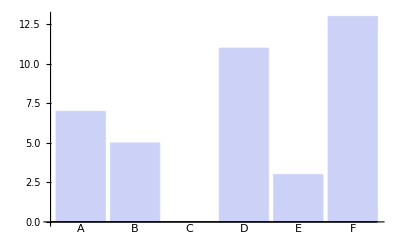

```mathematica
BarChart[("frequency"/.#)&/@loadedDieSpecification,ChartLabels->(("outcome"/.#)&/@loadedDieSpecification)]
```

```mathematica
testTally=Tally[nonUniformRandomSample[loadedDie,{100000}]]~Join~{{"C",0}}//SortBy[#,#⟦1⟧&]&
```

{{A,17865},{B,12962},{C,0},{D,28233},{E,7672},{F,33268}}

Formally checking the results would require a chi-squared test. Just go for "eyeballing" here:

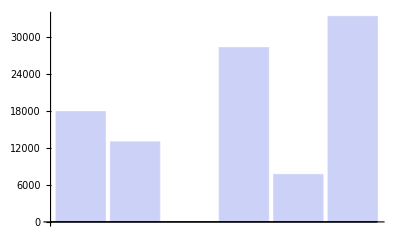

```mathematica
BarChart[#⟦2⟧&/@testTally,ChartLabels->#⟦1⟧&/@testTally]
```

### Frequentized Random Instruction Strings

```mathematica
redistributedInstructions=redistributeFrequencies[frequentizedInstructions]
```

{{outcome→commI,foreignOutcome→ur,frequency→0,foreignFrequency→1735},{outcome→conj2I,foreignOutcome→ul,frequency→0,foreignFrequency→1735},{outcome→conjI,foreignOutcome→true,frequency→0,foreignFrequency→1735},{outcome→det,foreignOutcome→Transpose,frequency→0,foreignFrequency→1735},{outcome→div,foreignOutcome→swap,frequency→0,foreignFrequency→1735},{outcome→inv,foreignOutcome→ST,frequency→0,foreignFrequency→1735},{outcome→nop,foreignOutcome→plus,frequency→0,foreignFrequency→1735},{outcome→tr,foreignOutcome→minus,frequency→140,foreignFrequency→1595},{outcome→pop,foreignOutcome→lr,frequency→280,foreignFrequency→1455},{outcome→rot,foreignOutcome→ll,frequency→280,foreignFrequency→1455},{outcome→uminus,foreignOutcome→false,frequency→280,foreignFrequency→1455},{outcome→plus,foreignOutcome→dup,frequency→1065,foreignFrequency→670},{outcome→ST,foreignOutcome→dot,frequency→1065,foreignFrequency→670},{outcome→swap,foreignOutcome→conj2,frequency→1065,foreignFrequency→670},{outcome→Transpose,foreignOutcome→conj,frequency→1065,foreignFrequency→670},{outcome→true,foreignOutcome→comm,frequency→1065,foreignFrequency→670},{outcome→ul,foreignOutcome→CHF,frequency→1065,foreignFrequency→670},{outcome→ur,foreignOutcome→dup,frequency→1065,foreignFrequency→670},{outcome→minus,foreignOutcome→dot,frequency→1205,foreignFrequency→530},{outcome→false,foreignOutcome→conj2,frequency→1345,foreignFrequency→390},{outcome→ll,foreignOutcome→conj,frequency→1345,foreignFrequency→390},{outcome→lr,foreignOutcome→comm,frequency→1345,foreignFrequency→390},{outcome→dup,foreignOutcome→CHF,frequency→1460,foreignFrequency→275},{outcome→dot,foreignOutcome→CHF,frequency→1600,foreignFrequency→135},{outcome→CHF,foreignOutcome→conj2,frequency→1720,foreignFrequency→15},{outcome→conj2,foreignOutcome→conj,frequency→1725,foreignFrequency→10},{outcome→conj,foreignOutcome→comm,frequency→1730,foreignFrequency→5},{outcome→comm,foreignOutcome→Null,frequency→1735,foreignFrequency→0}}

```mathematica
nRedistributedInstructions=Length@redistributedInstructions
```

28

```mathematica
heightRedistributedInstructions=
("frequency"/.(First@redistributedInstructions))+
("foreignFrequency"/.(First@redistributedInstructions))
```

1735

```mathematica
ClearAll[randomInstructionString];
randomInstructionString[n_:100]:=nonUniformRandomSample[
nRedistributedInstructions,
heightRedistributedInstructions,
redistributedInstructions,
{n}]
```

```mathematica
ClearAll[pretty];
pretty=Grid[T@{gridStack/@#}]&;
```

### Frequentized Random Instruction Combinations

Some random instruction strings generate VERY lengthy computations, much more than we want to tolerate. Some of these lengthy computations are due to symbolic inverses and determinants. We should not generate such things. Some of them are due to symbolic conjugate and commutator combinations. In reality, we only want conjugates and commutators for the primitive matrices with symbolic inputs. Therefore, we will restrict the searches to generating relevant instruction combinations.

```mathematica
execAllTrace[{},{ul,p,swap,comm}]
```

start | 
ul | 1 | 0
0 | 1 | 0 | 0
0 | 0
0 | 0
0 | 0 | 0 | 0
0 | 0
a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻 | 1 | 0
0 | 1 | 0 | 0
0 | 0
0 | 0
0 | 0 | 0 | 0
0 | 0 | a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻
swap | 1 | 0
0 | 1 | 0 | 0
0 | 0
0 | 0
0 | 0 | 0 | 0
0 | 0 | a | b
c | d | α | β
γ | δ
𝒜 | ℬ
𝒞 | 𝒟 | 𝔸 | 𝔹
ℂ | 𝔻
comm | a^2+b^2 | a c+b d
a c+b d | c^2+d^2 | a 𝒜+b ℬ | a 𝒞+b 𝒟
c 𝒜+d ℬ | c 𝒞+d 𝒟
0 | 0
0 | 0 | 0 | 0
0 | 0

```mathematica
ClearAll[frequentizedInstructionCombinations];
(frequentizedInstructionCombinations={
{"outcome"->{ul,swap,conj},"frequency"->25},
{"outcome"->{ur,swap,conj},"frequency"->25},
{"outcome"->{ll,swap,conj},"frequency"->25},
{"outcome"->{lr,swap,conj},"frequency"->25},
{"outcome"->{ul,swap,comm},"frequency"->25},
{"outcome"->{ur,swap,comm},"frequency"->25},
{"outcome"->{ll,swap,comm},"frequency"->25},
{"outcome"->{lr,swap,comm},"frequency"->25},
{"outcome"->{ul,swap,lr,conj2},"frequency"->8},
{"outcome"->{ul,swap,ll,conj2},"frequency"->8},
{"outcome"->{ul,swap,ur,conj2},"frequency"->8},
{"outcome"->{ur,swap,lr,conj2},"frequency"->8},
{"outcome"->{ur,swap,ll,conj2},"frequency"->8},
{"outcome"->{ur,swap,ul,conj2},"frequency"->8},
{"outcome"->{lr,swap,ur,conj2},"frequency"->8},
{"outcome"->{lr,swap,ll,conj2},"frequency"->8},
{"outcome"->{lr,swap,ul,conj2},"frequency"->8},
{"outcome"->{ll,swap,ur,conj2},"frequency"->8},
{"outcome"->{ll,swap,lr,conj2},"frequency"->8},
{"outcome"->{ll,swap,ul,conj2},"frequency"->8},
{"outcome"->{plus},"frequency"->100},
{"outcome"->{dot},"frequency"->100},
{"outcome"->{minus},"frequency"->100},
{"outcome"->{uminus},"frequency"->10},
{"outcome"->{tr},"frequency"->100},
{"outcome"->{T},"frequency"->100},
{"outcome"->{CHF},"frequency"->100},
{"outcome"->{ST},"frequency"->100},
{"outcome"->{dup},"frequency"->100},
{"outcome"->{swap},"frequency"->100},
{"outcome"->{rot},"frequency"->100},
{"outcome"->{pop},"frequency"->100},
{"outcome"->{true},"frequency"->100},
{"outcome"->{false},"frequency"->100},
{"outcome"->{ul},"frequency"->100},
{"outcome"->{ur},"frequency"->100},
{"outcome"->{ll},"frequency"->100},
{"outcome"->{lr},"frequency"->100}})//M;
```

```mathematica
redistributedInstructionCombinations=redistributeFrequencies@frequentizedInstructionCombinations;
```

```mathematica
nRedistributedInstructionCombinations=Length@redistributedInstructionCombinations
```

38

```mathematica
heightRedistributedInstructionCombinations=
("frequency"/.(First@redistributedInstructionCombinations))+
("foreignFrequency"/.(First@redistributedInstructionCombinations))
```

1003

```mathematica
ClearAll[randomInstructionCombinationString];
randomInstructionCombinationString[n_:100]:=nonUniformRandomSample[
nRedistributedInstructionCombinations,
heightRedistributedInstructionCombinations,
redistributedInstructionCombinations,
{n}]
```

```mathematica
ClearAll[pretty];
pretty=Grid[T@{gridStack/@#}]&;
```

## MONTE-CARLO SEARCH

```mathematica
caught={};
lastgood=commonbad=Table[{falsePunk},{4}];
count=0;score=0;
bin[bool_]:=If[bool,1,0];maxscore=0;
currentstring={};scorevec={0,0,0,0};
```

```mathematica
trial[]:=
With[{rc=2000,ln=100},
Block[{$RecursionLimit=rc},
With[{g=Join@@randomInstructionCombinationString[ln]},
currentstring=g;
With[{
tt=execAllRaw[{p,q},g],
tf=execAllRaw[{p,ST@q},g],
ft=execAllRaw[{ST@p,q},g],
ff=execAllRaw[{ST@p,ST@q},g]},
With[{result={tt,tf,ft,ff}},
If[Length@tt>0&&Length@tf>0&&Length@ft>0&&Length@ff>0,
score=0;
score+=(scorevec⟦1⟧=bin[falsey[tt⟦1⟧]]);
score+=(scorevec⟦2⟧=bin[truthy[tf⟦1⟧]]);
score+=(scorevec⟦3⟧=bin[truthy[ft⟦1⟧]]);
score+=(scorevec⟦4⟧=bin[truthy[ff⟦1⟧]]);
maxscore=Max[score,maxscore];
If[falsey[tt⟦1⟧]&&truthy[tf⟦1⟧]&&truthy[ft⟦1⟧]&&truthy[ff⟦1⟧],
AppendTo[caught,{g,result}]];
If[{#⟦1⟧}&/@result=!=commonbad,
pretty[lastgood=result],
pretty@lastgood]]]]]]]
```

```mathematica
Manipulate[foo,Button["Gen",foo=trial[]]]
```

```mathematica
Dynamic[
{count,score,scorevec,maxscore,currentstring,caught}]
```

```mathematica
Dynamic[pretty@lastgood]
```

```mathematica
count=0;Do[count++;trial[],{100000000}]
```

$Aborted

## I caught a fish!

```mathematica
ClearAll[fish,tt,tf,ft,ff];
fish={CHF,dot,iul,AMV,iul,plus,ill,iul,CY,ill,AMV};
tt=execAll[{p,q},fish];
tf=execAll[{p,ST@p},fish];
ft=execAll[{ST@p,q},fish];
ff=execAll[{ST@p,ST@q},fish];
{tt,tf,ft,ff}
(*Grid[MapThread[Map,{{pretty[{#}]&,falsey[#⟦1⟧]&,Length},Table[{tt,tf,ft,ff},{3}]}]]*)
```

{1+a x+c y | b x+d y
c w+a z | 1+d w+b z | 0 | 0
0 | 0
0 | 0
0 | 0 | 0 | 0
0 | 0,1 | 0
0 | 1 | 0 | 0
0 | 0
0 | 0
0 | 0 | 0 | 0
0 | 0,1 | 0
0 | 1 | 0 | 0
0 | 0
0 | 0
0 | 0 | 0 | 0
0 | 0,1 | 0
0 | 1 | 0 | 0
0 | 0
0 | 0
0 | 0 | 0 | 0
0 | 0}

```mathematica
execAll[{p,q},{CHF,dot}]
```

a x+c y | b x+d y
c w+a z | d w+b z | 0 | 0
0 | 0
a 𝒳+c 𝒴 | b 𝒳+d 𝒴
c 𝒲+a 𝒵 | d 𝒲+b 𝒵 | 0 | 0
0 | 0

```mathematica
execAll[{ST@p,ST@q},{CHF,dot,iul,AMV,iul,plus,ill,iul,CY,ill,AMV}]
```

1 | 0
0 | 1 | 0 | 0
0 | 0
0 | 0
0 | 0 | 0 | 0
0 | 0

```mathematica
PRENAND[m1_,m2_]:=iul+AMV[iul,m1.CHF[m2]]
```

```mathematica
Grid[{M/@MapThread[PRENAND,{{p,p,ap,ap},{q,aq,q,aq}}]}]
```

(1+a x+b z | b w+a y | 0 | 0
c x+d z | 1+d w+c y | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
AMV[CY[iul+AMV[iul,p.CHF[q]],ill,iul],ill]//M
```

Throw::nocatch: Uncaught Throw["NO NO NO"] returned to top level.

Hold[Throw[NO NO NO]]

## HORIZON

Don't look below this line.

## GENETIC SEARCH

```mathematica
ClearAll[
(* GLOBAL STATE *)
pool,generation,
(* TUNING PARAMETERS *)
generationSize,
geneLength,
mutationProbability,
maxRecombinationPoints,
(* FUNCTIONS & RULES *)
repool,fitness,symbolizer,run,bin,
scoreResult,swap,recombine,mutate];

generationSize=4*3;(* must be divisible by four *)
mutationProbability=0.10;
geneLength=40; (* can change! *)
maxRecombinationPoints=geneLength/10;

bin[bool_]:=If[bool,1,0];

repool[]:=pool=Table[randomString[geneLength],{generationSize}];
repool[];

symbolizer=Dispatch[{
iul->"iul",iur->"iur",
ill->"ill",ilr->"ilr",
plus->"+",minus->"-",dot->".",
true->"t",false->"f",
falsePunk->"f",truePunk->"t",
Transpose->"T"}];
scoreResult[{tt_,tf_,ft_,ff_}]:=Module[{score=0,scorevec=ConstantArray[0,4]},
If[Length@tt>0,
score=0;
score+=(scorevec⟦1⟧=bin[falsey[tt⟦1⟧]]);
score+=(scorevec⟦2⟧=bin[truthy[tf⟦1⟧]]);
score+=(scorevec⟦3⟧=bin[truthy[ft⟦1⟧]]);
score+=(scorevec⟦4⟧=bin[truthy[ff⟦1⟧]]);
];
{"score"->score,"scorevec"->scorevec}];
fitness[gene_]:=fitness[gene]=
Module[{score=0,scorevec=ConstantArray[0,4]},
With[{
tt=(clear[];push[p];push[q];exec[gene]),
tf=(clear[];push[p];push[aq];exec[gene]),
ft=(clear[];push[ap];push[q];exec[gene]),
ff=(clear[];push[ap];push[aq];exec[gene])},
With[{result={tt,tf,ft,ff}},
{"gene"->gene/.symbolizer,"result"->result/.symbolizer,
"length"->Length@gene}
~Join~(scoreResult@result)]]];
mutate[survivor_]:=
If[RandomReal[]<mutationProbability,
With[{position=RandomInteger[{1,"length"/.survivor}]},
With[{oldInstruction=("gene"/.survivor)⟦position⟧},
With[{newInstructionSet=Complement[instructionSet,{oldInstruction}]},
With[{newInstruction=RandomChoice[newInstructionSet]},
Module[{oldGene=("gene"/.survivor)},
(*Print[{position,oldInstruction,newInstruction,oldGene}/.symbolizer];*)
(oldGene⟦position⟧=newInstruction);
(*Print[{oldGene}/.symbolizer];*)
{"gene"->oldGene,
"length"->"length"/.survivor}]]]]],
survivor];
swap[{g1_,g2_},n_]:=
{g1⟦;;n⟧~Join~g2⟦n+1;;⟧,g2⟦;;n⟧~Join~g1⟦n+1;;⟧};
recombine[survivor1_,survivor2_]:=
With[{l=Min["length"/.survivor1,"length"/.survivor2]},
With[{rPoints=RandomInteger[{1,l},RandomInteger[{0,maxRecombinationPoints}]]//Union},
Fold[swap,{"gene"/.survivor1,"gene"/.survivor2},rPoints]]];
run[]:=
Module[{recombined,mutated,winners},
generation=Sort[
fitness/@pool,
{f,s}↦("score"/.f)>("score"/.s)];
winners=generation⟦;;generationSize/2⟧;
mutated=mutate/@winners;
If[Not@Divisible[generationSize,4],Throw["bad generationSize"]];
(*recombined=MapThread[recombine,{
mutated⟦;;generationSize/4⟧,
mutated⟦1+generationSize/4⟧;;}]//Flatten[#,1]&;*)
mutated
];
```

```mathematica
<<"Jacquard.m"
```

```mathematica
repool[];run[]/.symbolizer//Length
```

Throw::nocatch: Uncaught Throw["bad exec: {___}"] returned to top level.

Hold[Throw[bad exec: {___}]]

```mathematica
saveMe={{{CHF,dot,plus,{{1,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}},{{1,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}},pop,AMV,{{1,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}},plus,{{0,0,0,0},{0,0,0,0},{1,0,0,0},{0,1,0,0}},true,CY,{{0,0,0,0},{0,0,0,0},{1,0,0,0},{0,1,0,0}},AMV,{{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,1}},{{0,0,0,0},{0,0,0,0},{1,0,0,0},{0,1,0,0}},{{1,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}},pop,{{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,1}},{{1,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}}},{{{{0,0,0,0},{0,0,0,0},{1+a x+b z,b w+a y,0,0},{c x+d z,1+d w+c y,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,1}},{{0,0,0,0},{0,0,0,0},{1,0,0,0},{0,1,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,1}},{{1,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}}},{{{1,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,1}},{{0,0,0,0},{0,0,0,0},{1,0,0,0},{0,1,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,1}},{{1,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}}},{{{1,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,1}},{{0,0,0,0},{0,0,0,0},{1,0,0,0},{0,1,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,1}},{{1,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}}},{{{1,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,1}},{{0,0,0,0},{0,0,0,0},{1,0,0,0},{0,1,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,1}},{{1,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}}}}}};
```

### Other Primitive Operators

```mathematica
u3d=({{0, 0, 0, 0}, {1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}});u4d=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {1, 0, 0, 0}});iul=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
```

```mathematica
Dynamic@combos[u3d,p]
```

```mathematica
Dynamic@combos[u4d,p]
```

```mathematica
Dynamic@combos[u4d,p]
```